```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/phi3/2loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 23:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
convert=Table[ToExpression["topo"<>ToString[i]]-> ToExpression["IF"<>ToString[i]], {i,1,2}];
intfamvoc=Table[ToExpression["IF"<>ToString[i]],{i,1,2}];
```

## Integral family definition topo1

### Preliminaries

```mathematica
family = topo1;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
props ={ "props"->{k1,k2,k1+k2, k1-p,k2+p  }, "every prop is massive with mass^2 "->{m2}, "invariant is p^2 = pp"}
Export["./definitions/props.m",props]
MI={j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]} /. j[topo1,a__] -> topo1[a];
Export["./definitions/masters.m", MI]
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2+2 k2·p}

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

./definitions/props.m

./definitions/masters.m

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

```mathematica
intfam//TableForm
```

-m2+k1·k1
-m2+k2·k2
-m2+k1·k1+2 k1·k2+k2·k2
-m2+pp+k1·k1-2 k1·p
-m2+pp+k2·k2+2 k2·p

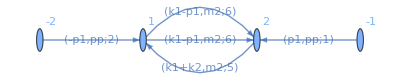

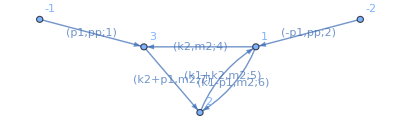

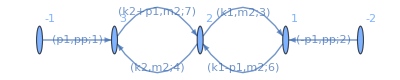

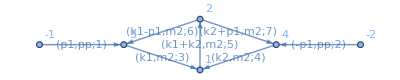

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

```mathematica
Get["./topo1/topo1"];
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*My Masters basis in d=2*)
mybasis= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],pp],
(*eyeball *)
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
pp(pp-4 m2)j[topo1,1,1,0,1,1],
pp j[topo1,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mpp=(D[R.T,pp].Inverse[R.T]//Simplify) + R.T.MppLiteRed.(Inverse[R.T])//PowerExpand//Simplify;
Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,-1,1,1,2,0]/(2 pp)-j[topo1,0,1,1,1,0]/(2 pp)-1/2 j[topo1,0,1,1,2,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],pp (-4 m2+pp) j[topo1,1,1,0,1,1],pp j[topo1,1,1,1,1,1]}

```mathematica
Mpp // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(√(4 m2-pp) √pp) | 0 | (2-d)/(8 m2-2 pp) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(3 (-2+d)^2)/(2 (m2-pp) (9 m2-pp) pp) | 0 | 0 | -((-3+d) ((4+d) m2+(-4+d) pp))/(2 pp (-9 m2+pp) (-m2+pp)) | -(9 d m2^2-60 m2 pp+10 d m2 pp+12 pp^2-3 d pp^2)/(18 m2^2 pp-20 m2 pp^2+2 pp^3) | 0 | 0 | 0
0 | (-2+d)/(2 √(4 m2-pp) √pp) | 0 | ((-6+d) m2)/(6 √(4 m2-pp) √pp) | -(5 m2 √pp)/(3 √(4 m2-pp)) | (2-d)/(8 m2-2 pp) | 0 | 0
0 | 0 | -(2 (-2+d))/(√(4 m2-pp) √pp) | 0 | 0 | 0 | (-2+d)/(-4 m2+pp) | 0
0 | (2-d)/(12 m2^3-7 m2^2 pp+m2 pp^2) | -((-2+d) (2 m2-pp))/(m2 (3 m2-pp) (4 m2-pp)^(3/2) √pp) | ((-18+7 d) m2-2 (-3+d) pp)/(3 m2 (12 m2^2-7 m2 pp+pp^2)) | (2 pp (m2+pp))/(3 m2 (3 m2-pp) (4 m2-pp)) | (4 (-3+d))/((3 m2-pp) (4 m2-pp)^(3/2) √pp) | (-3+d)/((3 m2-pp) (-4 m2+pp)^2) | (-4+d)/(2 (-3 m2+pp)))

### Preliminaries z

```mathematica
family = topo1Z;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{z,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=1/z;
```

```mathematica
{sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2} /. sp[a_,b_]-> a b
```

{k1^2-m2,k2^2-m2,k1^2+2 k1 k2+k2^2-m2,k1^2-m2-2 k1 p+1/z,k2^2-m2+2 k2 p+1/z}

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
props ={ "props"->{k1,k2,k1+k2, k1-p,k2+p  }, "every prop is massive with mass^2 "->{m2}, "invariant is p^2 = pp"}
Export["./definitions/props.m",props]
MI={j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]} /. j[topo1,a__] -> topo1[a];
Export["./definitions/masters.m", MI]
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+1/z+k1·k1-2 k1·p,-m2+1/z+k2·k2+2 k2·p}

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

./definitions/props.m

./definitions/masters.m

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1Z"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];
```

NewDsBasis::ovrw: Warning: definitions for topo1Z has been found. They may interfere with the upcoming definitions. Clearing definitions…

topo1Z is valid basis. The definitions of the basis will be saved in "topo1Z" directory.
    Ds[topo1Z] — denominators,
    SPs[topo1Z] — scalar products involving loop momenta,
    LMs[topo1Z] — loop momenta,
    EMs[topo1Z] — external momenta,
    Parameters[topo1Z] — parameters (invariants, masses, dimension),
    Toj[topo1Z] — rules to transform scalar products to denominators,
    CutDs[topo1Z] — flag vector of cut denominators.

topo1Z

Identities are generated.
    IBP[topo1Z] — integration-by-part identities,
    LI[topo1Z] — Lorentz invariance identities.

Found 8(24) zero(nonzero) sectors out of 32.
    ZeroSectors[topo1Z] — zero sectors,
    NonZeroSectors[topo1Z] — nonzero sectors,
    SimpleSectors[topo1Z] — simple sectors (no nonzero subsectors),
    BasisSectors[topo1Z] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[topo1Z] — a rule to nullify all zero j[topo1Z…],
    CutDs[topo1Z] — a flag list of cut denominators (1=cut).

Found 17 mapped sectors and 7 unique sectors.
    UniqueSectors[topo1Z] — unique sectors.
    MappedSectors[topo1Z] — mapped sectors.
    SR[topo1Z][…] — symmetry relations for j[topo1Z,…] from UniqueSectors[topo1Z].
    jSymmetries[topo1Z,…] — symmetry rules for the sector js[topo1Z,…] in UniqueSectors[topo1Z].
    jRules[topo1Z,…] — reduction rules for j[topo1Z,…] from MappedSectors[topo1Z].
    SectorsMappings[topo1Z] gives the list of mappings of all sectors from MappedSectors[topo1Z] to UniqueSectors[topo1Z].

Sector js[topo1Z,0,0,0,1,1]

Finished in 0 seconds.
    jRules[topo1Z, 0, 0, 0, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 0, 0, 0, 1, 1]).

Sector js[topo1Z,0,0,1,1,1]

Finished in 2 seconds.
    jRules[topo1Z, 0, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 0, 0, 1, 1, 1]).

Sector js[topo1Z,0,1,0,1,1]

Finished in 1 seconds.
    jRules[topo1Z, 0, 1, 0, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 0, 1, 0, 1, 1]).

Sector js[topo1Z,0,1,1,1,0]

Finished in 2 seconds.
    jRules[topo1Z, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 2 integrals (j[topo1Z, 0, 1, 1, 1, 0], j[topo1Z, 0, 2, 1, 1, 0]).

Sector js[topo1Z,0,1,1,1,1]

Finished in 2 seconds.
    jRules[topo1Z, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 0, 1, 1, 1, 1]).

Sector js[topo1Z,1,1,0,1,1]

Finished in 2 seconds.
    jRules[topo1Z, 1, 1, 0, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 1, 1, 0, 1, 1]).

Sector js[topo1Z,1,1,1,1,1]

Finished in 74 seconds.
    jRules[topo1Z, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[topo1Z] — list of master integrals appended with 1 integrals (j[topo1Z, 1, 1, 1, 1, 1]).

```mathematica
intfam//TableForm
```

-m2+k1·k1
-m2+k2·k2
-m2+k1·k1+2 k1·k2+k2·k2
-m2+1/z+k1·k1-2 k1·p
-m2+1/z+k2·k2+2 k2·p

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Get["./topo1Z/topo1Z"];
```

```mathematica
MIs[family]
```

{j[topo1Z,0,0,0,1,1],j[topo1Z,0,0,1,1,1],j[topo1Z,0,1,0,1,1],j[topo1Z,0,1,1,1,0],j[topo1Z,0,2,1,1,0],j[topo1Z,0,1,1,1,1],j[topo1Z,1,1,0,1,1],j[topo1Z,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1Z,0,0,0,1,1],j[topo1Z,0,0,1,1,1],j[topo1Z,0,1,0,1,1],j[topo1Z,0,1,1,1,0],j[topo1Z,0,2,1,1,0],j[topo1Z,0,1,1,1,1],j[topo1Z,1,1,0,1,1],j[topo1Z,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derz= Dinv[todiff,z];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derz, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderz=Collect[derz/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MzLiteRed = CoefficientArrays[redderz,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MIs[family]
```

{j[topo1Z,0,0,0,1,1],j[topo1Z,0,0,1,1,1],j[topo1Z,0,1,0,1,1],j[topo1Z,0,1,1,1,0],j[topo1Z,0,2,1,1,0],j[topo1Z,0,1,1,1,1],j[topo1Z,1,1,0,1,1],j[topo1Z,1,1,1,1,1]}

```mathematica
(*My Masters basis in d=2*)
mybasis= {  j[topo1Z,0,0,0,1,1],
m2 j[topo1Z,0,0,1,1,1],
Sqrt[4 m2 -1/z]Sqrt[1/z] j[topo1Z,0,1,0,1,1],
(* elliptic sector*)
j[topo1Z,0,1,1,1,0],
Dinv[j[topo1Z,0,1,1,1,0],z],
(*eyeball *)
(* m2 √(1/z(4 -1/z))*)j[topo1Z,0,1,1,1,1],
1/z(1/z-4 )j[topo1Z,1,1,0,1,1],
1/z j[topo1Z,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mz=(D[R.T,z].Inverse[R.T]//Simplify) + R.T.MzLiteRed.(Inverse[R.T])/.m2-> 1//PowerExpand//Simplify;
(*Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;*)
```

{j[topo1Z,0,0,0,1,1],m2 j[topo1Z,0,0,1,1,1],√(4 m2-1/z) √(1/z) j[topo1Z,0,1,0,1,1],j[topo1Z,0,1,1,1,0],-(1/2 z j[topo1Z,-1,1,1,2,0]-1/2 z j[topo1Z,0,1,1,1,0]+1/2 j[topo1Z,0,1,1,2,0])/z^2+j[topo1Z,0,1,1,2,0]/z^2,j[topo1Z,0,1,1,1,1],((-4+1/z) j[topo1Z,1,1,0,1,1])/z,j[topo1Z,1,1,1,1,1]/z}

```mathematica
Mz//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2-d)/(z √(-1+4 z)) | 0 | (2-d)/(2 z-8 z^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(3 (-2+d)^2)/(2 (-1+z) z (-1+9 z)) | 0 | 0 | -((-3+d) (-4+d+4 z+d z))/(2 (-1+z) z^2 (-1+9 z)) | (8-3 d-20 z+10 d z-36 z^2+9 d z^2)/(2 z-20 z^2+18 z^3) | 0 | 0 | 0
0 | (2-d)/(-2+8 z) | 0 | (6-d)/(-6+24 z) | (5 z)/(3-12 z) | (4-d-4 z)/(2 z-8 z^2) | 0 | 0
0 | 0 | (2 (-2+d))/(z √(-1+4 z)) | 0 | 0 | 0 | (2-d)/(z-4 z^2) | 0
0 | (-2+d)/(1-7 z+12 z^2) | ((-2+d) (-1+2 z))/((-1+3 z) (-1+4 z)^(3/2)) | -(6-2 d-18 z+7 d z)/(3 z-21 z^2+36 z^3) | (2 (1+z))/(3-21 z+36 z^2) | -(4 (-3+d))/(1-7 z+12 z^2) | -((-3+d) z)/((1-4 z)^2 (-1+3 z)) | (4-d)/(2 z-6 z^2))

```mathematica
Mz=Mz /.m2 -> 1;
```

```mathematica
Mz[[4;;6,4;;6]]/. d->2 -2ϵ//FullSimplify
```

{{0,1,0},{-((1+z (-3+ϵ)+ϵ) (1+2 ϵ))/((-1+z) z^2 (-1+9 z)),(1+3 ϵ-10 z ϵ-9 z^2 (1+ϵ))/(z (1-10 z+9 z^2)),0},{(2+ϵ)/(-3+12 z),(5 z)/(3-12 z),(1-2 z+ϵ)/(z-4 z^2)}}

```mathematica
{{0,1,0},{-((1+z (-3+ϵ)+ϵ) (1+2 ϵ))/((-1+z) z^2 (-1+9 z)),(1+3 ϵ-10 z ϵ-9 z^2 (1+ϵ))/(z (1-10 z+9 z^2)),0},{(2+ϵ)/(-3+12 z),(5 z)/(3-12 z),(1-2 z+ϵ)/(z-4 z^2)}}//MatrixForm
```

(0 | 1 | 0
-((1+z (-3+ϵ)+ϵ) (1+2 ϵ))/((-1+z) z^2 (-1+9 z)) | (1+3 ϵ-10 z ϵ-9 z^2 (1+ϵ))/(z (1-10 z+9 z^2)) | 0
(2+ϵ)/(-3+12 z) | (5 z)/(3-12 z) | (1-2 z+ϵ)/(z-4 z^2))

```mathematica
1-10z + 9 z^2 // Factor
3-10z + 9 z^2 // FullSimplify
```

(-1+z) (-1+9 z)

3+z (-10+9 z)

```mathematica
(1-z) (1-9 z)
```

```mathematica
(*My Masters basis in d=2*)
mybasis= {  j[topo1Z,0,0,0,1,1],
m2 j[topo1Z,0,0,1,1,1],
Sqrt[4 m2 -1/z]Sqrt[1/z] j[topo1Z,0,1,0,1,1],
(* elliptic sector*)
j[topo1Z,0,1,1,1,0],
Dinv[j[topo1Z,0,1,1,1,0],z],
(*eyeball *)
 m2 √(1/z(4 -1/z))j[topo1Z,0,1,1,1,1],
1/z(1/z-4 )j[topo1Z,1,1,0,1,1],
1/z j[topo1Z,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mz=(D[R.T,z].Inverse[R.T]//Simplify) + R.T.MzLiteRed.(Inverse[R.T])/.m2-> 1//PowerExpand//Simplify;
(*Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;*)
```

{j[topo1Z,0,0,0,1,1],m2 j[topo1Z,0,0,1,1,1],√(4 m2-1/z) √(1/z) j[topo1Z,0,1,0,1,1],j[topo1Z,0,1,1,1,0],-(1/2 z j[topo1Z,-1,1,1,2,0]-1/2 z j[topo1Z,0,1,1,1,0]+1/2 j[topo1Z,0,1,1,2,0])/z^2+j[topo1Z,0,1,1,2,0]/z^2,m2 √((4-1/z)/z) j[topo1Z,0,1,1,1,1],((-4+1/z) j[topo1Z,1,1,0,1,1])/z,j[topo1Z,1,1,1,1,1]/z}

```mathematica
Mz=Mz /.m2 -> 1;
```

```mathematica
Mz[[4;;6,4;;6]]/. d->2 -2ϵ//FullSimplify
```

{{0,1,0},{-((1+z (-3+ϵ)+ϵ) (1+2 ϵ))/((-1+z) z^2 (-1+9 z)),(1+3 ϵ-10 z ϵ-9 z^2 (1+ϵ))/(z (1-10 z+9 z^2)),0},{(2+ϵ)/(3 z √(-1+4 z)),-5/(3 √(-1+4 z)),ϵ/(z-4 z^2)}}

```mathematica
omega0Sunrise=Import["../../more_sectors/OnlyBaikov/periods/elliptic_sunrise_2l/periods_inf.m"] /. ρ -> z;
Δ = z/(1-10 z+9 z^2);
pfomega0=D[D[ω0[z],z],z] -> (-1+3 z)/((-1+z) z^2 (-1+9 z))ω0[z]  +(2-18 z^2)/(2 z-20 z^2+18 z^3)D[ω0[z],z] ;
```

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu  /. gtc -> Δ
```

{{1,ω1/ω0},{0,1}}

{{ω0,0},{dω0,gtc/ω0}}

{{ω0,ω1},{dω0,z/((1-10 z+9 z^2) ω0)+(dω0 ω1)/ω0}}

```mathematica
InvWss=Inverse[Wss]//Simplify
```

{{1/ω0,0},{-dω0/gtc,ω0/gtc}}

```mathematica
InvWss={{1/ω0[z],0},{-D[ω0[z],z]/Δ,ω0[z]/Δ}};
```

```mathematica
R1 = ({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, (-(-3+10 z+9 z^2) ω0[z] ω0[z])/(4 z^2), 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}}) .({{(d-2), 0, 0, 0, 0, 0, 0, 0}, {0, (d-2), 0, 0, 0, 0, 0, 0}, {0, 0, (d-2), 0, 0, 0, 0, 0}, {0, 0, 0, (d-2), 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2), 0, 0}, {0, 0, 0, 0, 0, 0, (d-2), 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)}}).({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1/ω0[z], 0, 0, 0, 0}, {0, 0, 0, -((1-10 z+9 z^2) ω0'[z])/z, ((1-10 z+9 z^2) ω0[z])/z, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
Collect[-R1[[4;;6,4;;6]]/2/. d->2-2 ϵ  , {_ω0,_ω0'},Together]
```

{{ϵ/ω0[z],0,0},{-((-3+10 z+9 z^2) ϵ ω0[z])/(4 z^2)+((1-10 z+9 z^2) ω0'[z])/(2 z),((-1+10 z-9 z^2) ω0[z])/(2 z),0},{0,0,ϵ}}

```mathematica
Mz1 = D[R1,z].Inverse[R1] + R1.Mz.Inverse[R1] /. pfomega0//Simplify;
```

```mathematica
Apart[(2-d)/(2 z-8 z^2)]/. d-> 2 -2 ep
```

ep/z-(4 ep)/(-1+4 z)

```mathematica
Mz1[[6]]//MatrixForm
```

(0
-(-2+d)/(2 z √(-1+4 z))
0
(-((18+20 z-198 z^2+d (-13+30 z+63 z^2)) ω0[z])/(z (1-10 z+9 z^2))-20 ω0'[z])/(12 √(-1+4 z))
-(5 (-2+d) z)/(3 √(-1+4 z) (1-10 z+9 z^2) ω0[z])
(2-d)/(2 z-8 z^2)
0
0)

```mathematica
Collect[Mz1[[4;;6,4;;6]]  /. d-> 2 -2 ϵ, {ϵ},FullSimplify]
% //MatrixForm
```

{{(9/(1-9 z)+1/(1-z)+3/(2 z)) ϵ,-(2 z ϵ)/((1-10 z+9 z^2) ω0[z]^2),0},{-((1+3 z)^4 ϵ ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)),(9/(1-9 z)+1/(1-z)+3/(2 z)) ϵ,0},{((-13+30 z+63 z^2) ϵ ω0[z])/(6 z √(-1+4 z) (1-10 z+9 z^2))+(2 ω0[z]-5 z ω0'[z])/(3 z √(-1+4 z)),(10 z ϵ)/(3 √(-1+4 z) (1-10 z+9 z^2) ω0[z]),ϵ/(z-4 z^2)}}

((9/(1-9 z)+1/(1-z)+3/(2 z)) ϵ | -(2 z ϵ)/((1-10 z+9 z^2) ω0[z]^2) | 0
-((1+3 z)^4 ϵ ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)) | (9/(1-9 z)+1/(1-z)+3/(2 z)) ϵ | 0
((-13+30 z+63 z^2) ϵ ω0[z])/(6 z √(-1+4 z) (1-10 z+9 z^2))+(2 ω0[z]-5 z ω0'[z])/(3 z √(-1+4 z)) | (10 z ϵ)/(3 √(-1+4 z) (1-10 z+9 z^2) ω0[z]) | ϵ/(z-4 z^2))

```mathematica
Mz1[[;;6]] /. d-> 2//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 ω0[z]-5 z ω0'[z])/(3 z √(-1+4 z)) | 0 | 0 | 0 | 0)

```mathematica
R2 = ({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, g[z]+(5 ω0[z])/(3 √(-1+4 z)), 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}})
R2Alt = ({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, g2[z], 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}})
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,g[z]+(5 ω0[z])/(3 √(-1+4 z)),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,g2[z],0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Collect[Mz1[[6]] /.d-> 2 -2 ep, {ep,_ω0',_ω0},Simplify]
Collect[Mz1[[6]] /.d-> 2 -2 ep, {ep,_ω0',_ω0},Simplify] /. ep -> 0
```

{0,ep/(z √(-1+4 z)),0,(2 ω0[z])/(3 z √(-1+4 z))+(ep (-13+30 z+63 z^2) ω0[z])/(6 z √(-1+4 z) (1-10 z+9 z^2))-(5 ω0'[z])/(3 √(-1+4 z)),(10 ep z)/(√(-1+4 z) (3-30 z+27 z^2) ω0[z]),ep/(z-4 z^2),0,0}

{0,0,0,(2 ω0[z])/(3 z √(-1+4 z))-(5 ω0'[z])/(3 √(-1+4 z)),0,0,0,0}

```mathematica
(2 ω0[z])/(3 z √(-1+4 z))-(5 ω0'[z])/(3 √(-1+4 z))
```

(2 ω0[z])/(3 z √(-1+4 z))-(5 ω0'[z])/(3 √(-1+4 z))

```mathematica
(2 ω0[z])/(3 z √(-1+4 z))-(10 ω0[z])/(3 (-1+4 z)^(3/2))//Simplify
```

-(2 (1+z) ω0[z])/(3 z (-1+4 z)^(3/2))

```mathematica
D[-(5 ω0[z])/(3 √(-1+4 z)),z]+(5 ω0'[z])/(3 √(-1+4 z)) //Simplify
```

(10 ω0[z])/(3 (-1+4 z)^(3/2))

```mathematica
Collect[(-((18+20 z-198 z^2+2 (-13+30 z+63 z^2)) ω0[z])/(z (1-10 z+9 z^2))-20 ω0'[z])/(12 √(-1+4 z)), {_ω0[z], _ω0'[z]}, Simplify]
```

(2 ω0[z]-5 z ω0'[z])/(3 z √(-1+4 z))

```mathematica
Mz2 = D[R2,z].Inverse[R2] + R2.Mz1.Inverse[R2] /. pfomega0//Simplify;
```

```mathematica
Collect[Mz2[[6,4]]/.g'[z]->(2 (1+z) ω0[z])/(3 z (-1+4 z)^(3/2))/. d-> 2 -2 ep//Simplify, {ep, ω0[z], g[z]},FullSimplify]
```

ep ((9/(1-9 z)+1/(1-z)+1/(-1/4+z)+1/(2 z)) g[z]+(4 (1+z) ω0[z])/(3 z (-1+4 z)^(3/2)))

```mathematica
Mz2[[6]] /.d-> 2-2ep;
Collect[%/.g'[z]->(2 (1+z) ω0[z])/(3 z (-1+4 z)^(3/2)), {ep,_g, _ω0},FullSimplify]
```

{0,ep/(z √(-1+4 z)),0,ep ((9/(1-9 z)+1/(1-z)+1/(-1/4+z)+1/(2 z)) g[z]+(4 (1+z) ω0[z])/(3 z (-1+4 z)^(3/2))),-(2 ep z g[z])/((1-10 z+9 z^2) ω0[z]^2),ep/(z-4 z^2),0,0}

```mathematica
Mz2Alt = D[R2Alt,z].Inverse[R2Alt] + R2Alt.Mz1.Inverse[R2Alt] /. pfomega0//Simplify;
```

```mathematica
Collect[Mz2Alt[[4;;6,4;;6]] /.g2'[z]->(-2 ω0[z]+5 z ω0'[z])/(3 z √(-1+4 z))/. d-> 2-2ep//Simplify ,{ep, _g2, _ω0},Together]/. ep -> ϵ 
% /. ep -> ϵ //MatrixForm
```

{{((3-10 z-9 z^2) ϵ)/(2 z (1-10 z+9 z^2)),-(2 z ϵ)/((1-10 z+9 z^2) ω0[z]^2),0},{-((1+3 z)^4 ϵ ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)),((3-10 z-9 z^2) ϵ)/(2 z (1-10 z+9 z^2)),0},{ϵ (((-1+2 z-13 z^2-36 z^3) g2[z])/(2 z (-1+4 z) (1-10 z+9 z^2))+((13-82 z+57 z^2+252 z^3) ω0[z])/(6 z (-1+4 z)^(3/2) (1-10 z+9 z^2))),ϵ (-(2 z g2[z])/((1-10 z+9 z^2) ω0[z]^2)+(10 z)/(3 √(-1+4 z) (1-10 z+9 z^2) ω0[z])),-ϵ/(z (-1+4 z))}}

(((3-10 z-9 z^2) ϵ)/(2 z (1-10 z+9 z^2)) | -(2 z ϵ)/((1-10 z+9 z^2) ω0[z]^2) | 0
-((1+3 z)^4 ϵ ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)) | ((3-10 z-9 z^2) ϵ)/(2 z (1-10 z+9 z^2)) | 0
ϵ (((-1+2 z-13 z^2-36 z^3) g2[z])/(2 z (-1+4 z) (1-10 z+9 z^2))+((13-82 z+57 z^2+252 z^3) ω0[z])/(6 z (-1+4 z)^(3/2) (1-10 z+9 z^2))) | ϵ (-(2 z g2[z])/((1-10 z+9 z^2) ω0[z]^2)+(10 z)/(3 √(-1+4 z) (1-10 z+9 z^2) ω0[z])) | -ϵ/(z (-1+4 z)))

### baikov analysis

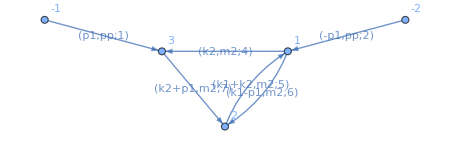

```mathematica
Import["./graphs/topo1/all/topo1_4_30.dot"]
```

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

d::shdw: Symbol d appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

m::shdw: Symbol m appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

p::shdw: Symbol p appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

q::shdw: Symbol q appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

s::shdw: Symbol s appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
(**)
edges = {{{1,2},m}, {{1,2},m}, {{1,3},m}, {{3,2},m}}
nodes ={{1,m},{3,m}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[Pi^2 baik/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) d[x1]⋀d[x2]⋀d[x3]⋀d[x4])/. eps-> 0] /. s-> pp
```

{{{1,2},m},{{1,2},m},{{1,3},m},{{3,2},m}}

{{{{1,2},m},{{1,2},m},{{1,3},m},{{3,2},m}},{{1,m},{3,m}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.051426

1/(√(3 m^4+2 m^2 x1-x1^2+2 m^2 x2+2 x1 x2-x2^2+2 m^2 x4+2 x1 x4+2 x2 x4-x4^2) √(4 m^2 pp-pp^2+2 pp x3-x3^2+2 pp x4+2 x3 x4-x4^2))

```mathematica
(* the sector is not elliptic, in fact *)
baik /. {x1-> 0, x2 -> 0, x3 -> 0, x4 -> 0}//PowerExpand//Factor//PowerExpand
(* which is the correct leading singularity 
m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1]
*)
```

1/(√3 m^2 √(4 m^2-pp) √pp)

```mathematica
(* let's release cut corresponding to x3, this select a tadpole subtopology *)
integrand=baik/x3 /. {x1-> 0, x2 -> 0, x4 -> 0}//PowerExpand//Factor//PowerExpand
int1=Integrate[%,x3]//TrigToExp
logs = Union@Cases[int1,_Log,∞ ];
leadSing=Coefficient[int1,logs]
Total[leadSing]
```

1/(√3 m^2 x3 √(4 m^2 pp-pp^2+2 pp x3-x3^2))

(ⅈ Log[1-(ⅈ √(-4 m^2+pp) √(4 m^2 pp-(pp-x3)^2))/(√pp (-4 m^2+pp-x3))])/(2 √3 m^2 √pp √(-4 m^2+pp))-(ⅈ Log[1+(ⅈ √(-4 m^2+pp) √(4 m^2 pp-(pp-x3)^2))/(√pp (-4 m^2+pp-x3))])/(2 √3 m^2 √pp √(-4 m^2+pp))

{ⅈ/(2 √3 m^2 √pp √(-4 m^2+pp)),-ⅈ/(2 √3 m^2 √pp √(-4 m^2+pp))}

0

```mathematica
(* there is no pole at infinity *)
(integrand/. x3 -> 1/x3)/x3/x3 //FullSimplify //Together//PowerExpand
(* I can take the residue in x3 around 0 or integrating along the branch... easy residue :) *)
Residue[integrand,{x3,0}]
```

-ⅈ/(√3 m^2 √(1-2 pp x3-4 m^2 pp x3^2+pp^2 x3^2))

1/(√3 m^2 √((4 m^2-pp) pp))

```mathematica
(* let's release the cut corresponding to x4, this select the sunrise subtopology *)
integrand=baik/x4 /. {x1-> 0, x2 -> 0, x3 -> 0}//PowerExpand//Factor//PowerExpand
```

1/(x4 √(3 m^4+2 m^2 x4-x4^2) √(4 m^2 pp-pp^2+2 pp x4-x4^2))

```mathematica
(* Now I have a pole in x4 around 0, taking the residue around it corresponds to taking the max cut again *)
(* the two sqaure root introduce now a more complicated structure. *)
(* there are four solution for the polynomials under root
 3 m^4+2 m^2 x4-x4^2 == 0         --->   {x4->-m^2,x4->3 m^2}
4 m^2 pp-pp^2+2 pp x4-x4^2 == 0  --->   {x4->-2 m √pp+pp,x4->2 m √pp+pp}
*)
```

```mathematica
(* first of all, the sunrise has baikov given by *)
(*(**)
edges = {{{1,2},m}, {{1,2},m}, {{1,2},m}}
nodes ={{1,m},{2,m}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[Pi^2 baik/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4] d[x1]⋀d[x2]⋀d[x3]⋀d[x4])/. eps-> 0] /. s-> pp *)
sunbaik=1/√(-m^4+2 m^2 pp-pp^2-2 m^2 x2+2 pp x2-x2^2+2 m^2 x4+2 pp x4+2 x2 x4-x4^2) /√(-x1^2+2 x1 x3-x3^2+4 m^2 x4+2 x1 x4+2 x3 x4-x4^2)// FullSimplify;
(* which integrates to *)
int1=Integrate[sunbaik/x1/x2/x3, x1]//TrigToExp;
logs = Union@Cases[int1, _Log,∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2,x3]//TrigToExp;
logs = Union@Cases[int2, _Log,∞];
toint3=Coefficient[int2,logs][[1]];
int3 = Integrate[toint3,x2]//TrigToExp;
logs = Union@Cases[int3, _Log,∞];
sunriseELL=Coefficient[int3,logs][[1]]//FullSimplify
```

ⅈ/(4 √(4 m^2-x4) √x4 √(m^4+(pp-x4)^2-2 m^2 (pp+x4)))

```mathematica
(* if we forget for a second of the x4 pole, the two integrands are the same up to a shift, it must be so ofc, you get the sunrise by forgetting about 1/x4 in the general integral *)
```

```mathematica
integrand // FullSimplify // PowerExpand // FullSimplify
sunriseELL /. x4 -> x4 +m^2//FullSimplify//PowerExpand//FullSimplify
```

1/(√(4 m^2 pp-(pp-x4)^2) √(3 m^2-x4) x4 √(m^2+x4))

ⅈ/(4 √(-4 m^2 pp+(pp-x4)^2) √(3 m^2-x4) √(m^2+x4))

```mathematica
(* We know that we could write a second order PF operator for this integral, it does have a MUM point at pp = 0,
and Froebenius method tells us how to find two independent solutions. One is the holomorphic solution. We can find the holomorphic solution by expanding for pp -> 0  and taking residues again. There is onlly ONE non trivial integration possible for a closed contour, and that must correspond to the holomorphic solution *)
tmpseries=Collect[Series[sunriseELL /. m-> 1 /. pp -> ρ, {ρ,0,15}]//Normal // PowerExpand , {ρ}, FullSimplify]//PowerExpand;
```

```mathematica
sunriseELL /. m-> 1 /. pp -> ρ
```

ⅈ/(4 √(4-x4) √x4 √(1+(-x4+ρ)^2-2 (x4+ρ)))

```mathematica
(* we don't have anymore the four solution, two of them degenerate into a pole. Global residue theorem, I can integrate around the pole, which is in x4 -> 1 *)
(Residue[Series[tmpseries/((-ⅈ/(2 √3))), {x4,1,-1}, Assumptions->{x4<0}]//Normal, {x4,1}]//Expand)
ω0s=Import["./PERIODS/omega0.m"];
ω0s[[1]] /. extractPolySol /. ρ^a_ /; a> 15 -> 0
```

-1/2-ρ/6-(5 ρ^2)/54-(31 ρ^3)/486-(71 ρ^4)/1458-(517 ρ^5)/13122-(11723 ρ^6)/354294-(10105 ρ^7)/354294-(26639 ρ^8)/1062882-(5773279 ρ^9)/258280326-(15629785 ρ^10)/774840978-(128162555 ρ^11)/6973568802-(1059293225 ρ^12)/62762119218-(2938020985 ρ^13)/188286357654-(24586482605 ρ^14)/1694577218886-(620302718677 ρ^15)/45753584909922

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147+(10105 ρ^7)/177147+(26639 ρ^8)/531441+(5773279 ρ^9)/129140163+(15629785 ρ^10)/387420489+(128162555 ρ^11)/3486784401+(1059293225 ρ^12)/31381059609+(2938020985 ρ^13)/94143178827+(24586482605 ρ^14)/847288609443+(620302718677 ρ^15)/22876792454961

```mathematica
integrand
```

1/(x4 √(3 m^4+2 m^2 x4-x4^2) √(4 m^2 pp-pp^2+2 pp x4-x4^2))

```mathematica
(* What about the integrand from the supersector? *)
tmpseries=Collect[Series[integrand (*Sqrt[4 -ρ]Sqrt[ρ]*)/. m-> 1 /. pp -> ρ, {ρ,0,20}]//Normal // PowerExpand , {ρ}, FullSimplify]//PowerExpand;
(* we don't have anymore the four solution, two of them degenerate into a pole. Global residue theorem, I can integrate around the pole, which is in x4 -> 0 *)
function=(Residue[Series[tmpseries/((-ⅈ/(3 √3))), {x4,0,-1}, Assumptions->{x4<0}]//Normal, {x4,0}]//Expand)
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]]
```

1+(5 ρ)/9+ρ^2/3+(55 ρ^3)/243+(1111 ρ^4)/6561+(887 ρ^5)/6561+(19955 ρ^6)/177147+(17119 ρ^7)/177147+(4999 ρ^8)/59049+(9729985 ρ^9)/129140163+(78903455 ρ^10)/1162261467+(7978325 ρ^11)/129140163+(1778819513 ρ^12)/31381059609+(133110683501 ρ^13)/2541865828329+(123693617443 ρ^14)/2541865828329+(1039708833757 ρ^15)/22876792454961+(2925904349005 ρ^16)/68630377364883+(918418168387 ρ^17)/22876792454961+(1897904061292487 ρ^18)/50031545098999707+(16189191797078305 ρ^19)/450283905890997363+(5128617885346009 ρ^20)/150094635296999121

F2[g[ρ,0]]+5/9 F2[g[ρ,1]]+1/3 F2[g[ρ,2]]+55/243 F2[g[ρ,3]]+(1111 F2[g[ρ,4]])/6561+(887 F2[g[ρ,5]])/6561+(19955 F2[g[ρ,6]])/177147+(17119 F2[g[ρ,7]])/177147+(4999 F2[g[ρ,8]])/59049+(9729985 F2[g[ρ,9]])/129140163+(78903455 F2[g[ρ,10]])/1162261467+(7978325 F2[g[ρ,11]])/129140163+(1778819513 F2[g[ρ,12]])/31381059609+(133110683501 F2[g[ρ,13]])/2541865828329+(123693617443 F2[g[ρ,14]])/2541865828329+(1039708833757 F2[g[ρ,15]])/22876792454961+(2925904349005 F2[g[ρ,16]])/68630377364883+(918418168387 F2[g[ρ,17]])/22876792454961+(1897904061292487 F2[g[ρ,18]])/50031545098999707+(16189191797078305 F2[g[ρ,19]])/450283905890997363+(5128617885346009 F2[g[ρ,20]])/150094635296999121

```mathematica
(* 
Waht is the function? We expect to find an integral formula, so most likely a differential equation satisfied by it 
*)
```

```mathematica
maxorder=3
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] ω0s[[1]]+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[ω0s[[1]] /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

3

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,20],0]//Solve//Flatten
```

{a[3]→-a[1]/4-a[2]/2,b[1]→2 a[1],b[2]→a[1]/2+2 a[2],b[3]→-a[1]/4-a[2]/2,c[1]→-a[1],c[2]→-a[1]/2-a[2],c[3]→0,d[1]→0,d[2]→-(5 a[1])/2,d[3]→-(5 a[1])/4-(5 a[2])/2}

```mathematica
(* the following operator annihilates the function (careful with the inhomogenous term)*)
ansatzDerSol= ansatzDer /. sol /. F1[]-> 1 /. F1[θ] -> θ ;
inhomogSol=   Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}]dω0/. sol;
op=ansatzDerSol +inhomogSol   /. a[1] ->1//Factor
OP = Collect[-1/2 ρ (-2-4 F1[θ]+ρ+F1[θ] ρ), {_F1, ω0, dω0}]
inhomog =-1/2 ρ(+5 dω0 ρ+2 ω0)
```

-1/4 ρ (-2-4 θ+ρ+5 dω0 ρ+θ ρ+2 ω0) (2+ρ+2 ρ a[2])

-1/2 (-2+ρ) ρ-1/2 (-4+ρ) ρ F1[θ]

-1/2 ρ (5 dω0 ρ+2 ω0)

```mathematica
Collect[Solve[-1/2 (-2+ρ) ρ F-1/2 (-4+ρ) ρ^2 derF  -1/2 ρ (5 dω0 ρ+2 ω0)== 0 ,derF], {ω0, dω0}]
```

{{derF→-(5 dω0)/(-4+ρ)+(2 F-F ρ)/((-4+ρ) ρ)-(2 ω0)/((-4+ρ) ρ)}}

```mathematica
(* the function satisfies the differential equation

derF =-(5 dω0)/(-4+ρ)+(2 F-F ρ)/((-4+ρ) ρ)-(2 ω0)/((-4+ρ) ρ)

 *)
```

```mathematica
(* lets go in step, first we normalize the integral by its leading singularity (max cut) *)
(*√((4 m^2-pp) pp)*)
(* and remove also dω0 *)
```

```mathematica
tmp=Collect[D[Sqrt[4 - ρ]Sqrt[ρ] F[ρ]- ω0[ρ](5 ρ)/(√(-((-4+ρ) ρ))),ρ] /. F'[ρ] ->-(5 dω0)/(-4+ρ)+(2 F[ρ]-F[ρ] ρ)/((-4+ρ) ρ)-(2 ω0)/((-4+ρ) ρ) /. F[ρ]-> F[ρ]/(Sqrt[4 - ρ]Sqrt[ρ]) /.ω0'[ρ]-> dω0 /.  ω0[ρ] -> ω0 , {_F,ω0,dω0 }, FullSimplify]
```

-(2 ρ (1+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
g4def = g4'[ρ]->(2 ρ (1+ρ) ω0)/(3 (((4-ρ) ρ))^(3/2));
```

### Shift d -> d+2

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m12,m22,m32,m42,m52},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m12, sp[k2,k2]-m22, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m32,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m42,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m52}
```

{-m12+k1·k1,-m22+k2·k2,-m32+k1·k1+2 k1·k2+k2·k2,-m42+pp+k1·k1-2 k1·p,-m52+pp+k2·k2+2 k2·p}

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[familyAllMass,intfam,{k1,k2},Directory->"topoAllMass"]

GenerateIBP[familyAllMass];

AnalyzeSectors[familyAllMass];

FindSymmetries[familyAllMass];

(*Save to disk*)
DiskSave[familyAllMass];
```

familyAllMass is valid basis. The definitions of the basis will be saved in "topoAllMass" directory.
    Ds[familyAllMass] — denominators,
    SPs[familyAllMass] — scalar products involving loop momenta,
    LMs[familyAllMass] — loop momenta,
    EMs[familyAllMass] — external momenta,
    Parameters[familyAllMass] — parameters (invariants, masses, dimension),
    Toj[familyAllMass] — rules to transform scalar products to denominators,
    CutDs[familyAllMass] — flag vector of cut denominators.

familyAllMass

Identities are generated.
    IBP[familyAllMass] — integration-by-part identities,
    LI[familyAllMass] — Lorentz invariance identities.

Found 8(24) zero(nonzero) sectors out of 32.
    ZeroSectors[familyAllMass] — zero sectors,
    NonZeroSectors[familyAllMass] — nonzero sectors,
    SimpleSectors[familyAllMass] — simple sectors (no nonzero subsectors),
    BasisSectors[familyAllMass] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[familyAllMass] — a rule to nullify all zero j[familyAllMass…],
    CutDs[familyAllMass] — a flag list of cut denominators (1=cut).

Found 0 mapped sectors and 24 unique sectors.
    UniqueSectors[familyAllMass] — unique sectors.
    MappedSectors[familyAllMass] — mapped sectors.
    SR[familyAllMass][…] — symmetry relations for j[familyAllMass,…] from UniqueSectors[familyAllMass].
    jSymmetries[familyAllMass,…] — symmetry rules for the sector js[familyAllMass,…] in UniqueSectors[familyAllMass].
    jRules[familyAllMass,…] — reduction rules for j[familyAllMass,…] from MappedSectors[familyAllMass].
    SectorsMappings[familyAllMass] gives the list of mappings of all sectors from MappedSectors[familyAllMass] to UniqueSectors[familyAllMass].

```mathematica
intfam  = {SP[k1,k1]-m12, SP[k2,k2]-m22, SP[k1,k1]+SP[k2,k2] + 2 SP[k1,k2]-m32,SP[k1,k1]+SP[p,p] - 2 SP[k1,p]-m42,SP[k2,k2]+SP[p,p] +2 SP[k2,p]-m52}
```

{-m12+SP[k1,k1],-m22+SP[k2,k2],-m32+SP[k1,k1]+2 SP[k1,k2]+SP[k2,k2],-m42+SP[k1,k1]-2 SP[k1,p]+SP[p,p],-m52+SP[k2,k2]+2 SP[k2,p]+SP[p,p]}

```mathematica
propsFull
```

propsFull

```mathematica
propsFull = Sum[intfam[[i]]u[ToExpression["m"<>ToString[i]<>"2"]], {i,1,5}];
delta = Coefficient[propsFull, SP[k1,k1]]Coefficient[propsFull, SP[k2,k2]]-Coefficient[propsFull, SP[k1,k2]]Coefficient[propsFull, SP[k1,k2]]/4//Expand //Simplify
```

u[m32] u[m42]+u[m22] (u[m32]+u[m42])+u[m32] u[m52]+u[m42] u[m52]+u[m12] (u[m22]+u[m32]+u[m52])

```mathematica
mybasisd2= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],pp],
(* rest *)
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
pp(pp-4 m2)j[topo1,1,1,0,1,1],
 eps(3-d)/(6-d)^2 pp j[topo1,1,1,1,1,1]}
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,-1,1,1,2,0]/(2 pp)-j[topo1,0,1,1,1,0]/(2 pp)-1/2 j[topo1,0,1,1,2,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],pp (-4 m2+pp) j[topo1,1,1,0,1,1],((3-d) eps pp j[topo1,1,1,1,1,1])/(6-d)^2}

```mathematica
mybasis=Join[IBPReduce[((  (2^2)/(6-d)^2 delta mybasisd2[[;;7]]//Expand )/.topo1 -> familyAllMass)  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1]//Simplify,{mybasisd2[[8]]}];
```

```mathematica
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
invT = Inverse[T]//Simplify;
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
(* rescale epsilon dependence *)
newMpp[2] =EPS.newMpp[1] .Inverse[EPS] // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(((-4+Global`d+2 eps) (-3 dω0 (27-21 ρ-7 ρ^2+ρ^3) (-45+20 ρ+ρ^2-Global`d (-9+ρ^2)+3 eps (9-10 ρ+ρ^2))+(729-1170 ρ+472 ρ^2-30 ρ^3-ρ^4-108 eps^2 (-45+59 ρ-15 ρ^2+ρ^3)-3 eps (3429-2190 ρ+308 ρ^2-18 ρ^3+7 ρ^4)+3 Global`d (-9+ρ^2) (9-10 ρ+ρ^2+eps (-87+22 ρ+ρ^2))) ω0))/(2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ ω0) | (9 eps (3 (Global`d)^2 (-3+ρ) (3+ρ)^2-54 eps^2 (9-10 ρ+ρ^2)+6 eps (297-168 ρ-35 ρ^2+2 ρ^3)+4 (-405+54 ρ+59 ρ^2+4 ρ^3)-3 Global`d (3+ρ) (-81+20 ρ+5 ρ^2+eps (45-30 ρ+ρ^2))))/(2 (2-9 eps+9 eps^2) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0^2)
-(3 dω0^2 (-4+Global`d+2 eps) (3+ρ) (9-10 ρ+ρ^2)^2 (45-20 ρ-ρ^2+Global`d (-9+ρ^2)-3 eps (9-10 ρ+ρ^2))+dω0 (9-10 ρ+ρ^2) (6 (Global`d)^2 (-9+ρ^2) (9-10 ρ+ρ^2+eps (-87+22 ρ+ρ^2))-8 (810-1170 ρ+354 ρ^2+10 ρ^3-4 ρ^4+54 eps^3 (-45+59 ρ-15 ρ^2+ρ^3)-3 eps^2 (-3456+3219 ρ-517 ρ^2-15 ρ^3+ρ^4)-eps (11016-7155 ρ+629 ρ^2+111 ρ^3+7 ρ^4))+Global`d (4 (891-1125 ρ+177 ρ^2+65 ρ^3-8 ρ^4)-3 eps^2 (-6615+5040 ρ-342 ρ^2-136 ρ^3+5 ρ^4)-3 eps (13689-6324 ρ-506 ρ^2+300 ρ^3+9 ρ^4))) ω0+(-864 eps^4 (-5+ρ)^2 (9-10 ρ+ρ^2)+20 (-3+ρ) (9-10 ρ+ρ^2)^2+24 eps^3 (38205-46338 ρ+15958 ρ^2-1688 ρ^3+5 ρ^4+2 ρ^5)+2 eps^2 (-566757+599103 ρ-200426 ρ^2+20662 ρ^3-49 ρ^4+11 ρ^5)+2 eps (76869-137187 ρ+73082 ρ^2-13390 ρ^3+609 ρ^4+17 ρ^5)+3 (Global`d)^2 (-3+ρ) (9-10 ρ+ρ^2+eps (-87+22 ρ+ρ^2))^2-Global`d (17 (-3+ρ) (9-10 ρ+ρ^2)^2+12 eps^3 (19575-21915 ρ+7110 ρ^2-662 ρ^3-13 ρ^4+ρ^5)+3 eps^2 (-188973+182427 ρ-55882 ρ^2+4990 ρ^3+87 ρ^4+7 ρ^5)+2 eps (48033-83799 ρ+43314 ρ^2-7894 ρ^3+333 ρ^4+13 ρ^5))) ω0^2)/(18 eps (2-9 eps+9 eps^2) (-9+ρ)^2 (-1+ρ)^2) | (-3 dω0 (-4+Global`d+2 eps) (27-21 ρ-7 ρ^2+ρ^3) (45-20 ρ-ρ^2+Global`d (-9+ρ^2)-3 eps (9-10 ρ+ρ^2))+(216 eps^3 (-45+59 ρ-15 ρ^2+ρ^3)+4 (891-1170 ρ+236 ρ^2+50 ρ^3-7 ρ^4)-6 eps^2 (-7155+6438 ρ-680 ρ^2-150 ρ^3+11 ρ^4)+2 eps (-22761+14310 ρ-196 ρ^2-582 ρ^3+13 ρ^4)-3 (Global`d)^2 (-9+ρ^2) (9-10 ρ+ρ^2+eps (-87+22 ρ+ρ^2))+Global`d (-1863+2250 ρ-236 ρ^2-170 ρ^3+19 ρ^4+6 eps (3483-1581 ρ-215 ρ^2+105 ρ^3)+3 eps^2 (-3429+2520 ρ+6 ρ^2-128 ρ^3+7 ρ^4))) ω0)/(2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ ω0))

```mathematica
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ρ (8+4 eps (-3+ρ)-4 ρ+Global`d (-2-eps (-4+ρ)+ρ)))/((-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0
-(3 (-4+Global`d+2 eps) (Global`d (3+ρ) (54-22 ρ-6 eps^2 (-72+30 ρ+ρ^2)+3 eps^3 (-63+30 ρ+ρ^2)+eps (-297+116 ρ+3 ρ^2))+2 (-324+123 ρ+16 ρ^2+ρ^3-54 eps^4 (9-10 ρ+ρ^2)-6 eps^3 (-378+285 ρ-4 ρ^2+ρ^3)-2 eps (-972+405 ρ+47 ρ^2+4 ρ^3)+eps^2 (-3402+1845 ρ+104 ρ^2+13 ρ^3))))/(2 (-1+eps)^2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ ω0) | 0 | 0 | (6 dω0 (-4+Global`d+2 eps) ρ (27-21 ρ-7 ρ^2+ρ^3) (45-20 ρ-ρ^2+Global`d (-9+ρ^2)-3 eps (9-10 ρ+ρ^2))-(54 eps^3 (81-360 ρ+354 ρ^2-80 ρ^3+5 ρ^4)-2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (81-40 ρ-ρ^2+3 Global`d (-9+ρ^2))-3 eps^2 (5346-23760 ρ+19980 ρ^2-5208 ρ^3+610 ρ^4-40 ρ^5+Global`d (-1215+5427 ρ-3942 ρ^2+822 ρ^3-75 ρ^4+7 ρ^5))+eps (3 (Global`d)^2 (-3+ρ)^2 (27-117 ρ-39 ρ^2+ρ^3)+3 Global`d (-2187+10827 ρ-5490 ρ^2+306 ρ^3+125 ρ^4+3 ρ^5)-4 (-3645+17739 ρ-12024 ρ^2+2784 ρ^3-275 ρ^4+29 ρ^5))) ω0)/(4 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | -(9 eps (-3 (Global`d)^2 (-3+ρ) (3+ρ)^2+54 eps^2 (9-10 ρ+ρ^2)-6 eps (297-168 ρ-35 ρ^2+2 ρ^3)-4 (-405+54 ρ+59 ρ^2+4 ρ^3)+3 Global`d (3+ρ) (-81+20 ρ+5 ρ^2+eps (45-30 ρ+ρ^2))))/(2 (2-9 eps+9 eps^2) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0^2) | 0 | 0 | 0
(2 dω0 (-4+Global`d+2 eps) ρ (9-10 ρ+ρ^2) (Global`d (3+ρ) (54-22 ρ-6 eps^2 (-72+30 ρ+ρ^2)+3 eps^3 (-63+30 ρ+ρ^2)+eps (-297+116 ρ+3 ρ^2))+2 (-324+123 ρ+16 ρ^2+ρ^3-54 eps^4 (9-10 ρ+ρ^2)-6 eps^3 (-378+285 ρ-4 ρ^2+ρ^3)-2 eps (-972+405 ρ+47 ρ^2+4 ρ^3)+eps^2 (-3402+1845 ρ+104 ρ^2+13 ρ^3)))+(-216 eps^6 (81-360 ρ+354 ρ^2-80 ρ^3+5 ρ^4)-4 (-4+Global`d) ρ (9-10 ρ+ρ^2) (72-25 ρ-ρ^2+Global`d (-27+11 ρ))-6 eps^5 (Global`d (3159-15309 ρ+12150 ρ^2-2010 ρ^3-45 ρ^4+7 ρ^5)-4 (4860-22329 ρ+19548 ρ^2-3702 ρ^3+80 ρ^4+7 ρ^5))+eps^2 (4 (-37908+215919 ρ-177516 ρ^2+35538 ρ^3+72 ρ^4-137 ρ^5)+32 Global`d (2187-13257 ρ+10809 ρ^2-2361 ρ^3+32 ρ^4+6 ρ^5)-(Global`d)^2 (8019-51003 ρ+40824 ρ^2-9468 ρ^3+221 ρ^4+15 ρ^5))+2 eps ((Global`d)^2 (729-6615 ρ+6714 ρ^2-1952 ρ^3+97 ρ^4+3 ρ^5)+4 (2916-22491 ρ+22005 ρ^2-5507 ρ^3+111 ρ^4+22 ρ^5)-Global`d (5832-49275 ρ+49392 ρ^2-13550 ρ^3+528 ρ^4+33 ρ^5))+2 eps^3 (Global`d (-61965+336042 ρ-256950 ρ^2+48680 ρ^3+235 ρ^4-122 ρ^5)+3 (Global`d)^2 (1944-11097 ρ+8163 ρ^2-1641 ρ^3+5 ρ^4+2 ρ^5)+8 (19683-100683 ρ+79722 ρ^2-14261 ρ^3-159 ρ^4+50 ρ^5))+eps^4 (-3 (Global`d)^2 (1701-9315 ρ+6858 ρ^2-1278 ρ^3-15 ρ^4+ρ^5)+12 Global`d (7047-36018 ρ+27657 ρ^2-4827 ρ^3-80 ρ^4+13 ρ^5)-4 (71442-343845 ρ+280242 ρ^2-49260 ρ^3-196 ρ^4+145 ρ^5))) ω0)/(12 (-1+eps)^2 eps (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ) | 0 | 0 | (-12 dω0^2 (-4+Global`d+2 eps) ρ^2 (3+ρ) (9-10 ρ+ρ^2)^2 (45-20 ρ-ρ^2+Global`d (-9+ρ^2)-3 eps (9-10 ρ+ρ^2))+4 dω0 (-4+Global`d+2 eps) ρ (9-10 ρ+ρ^2) (27 eps^2 (81-360 ρ+354 ρ^2-80 ρ^3+5 ρ^4)-2 ρ (9-10 ρ+ρ^2) (90-30 ρ-4 ρ^2+3 Global`d (-9+ρ^2))+3 eps (-1215+5886 ρ-3618 ρ^2+456 ρ^3+25 ρ^4+2 ρ^5+Global`d (-3+ρ)^2 (27-117 ρ-39 ρ^2+ρ^3))) ω0+(-4 (20-17 Global`d+3 (Global`d)^2) (-3+ρ) ρ^2 (9-10 ρ+ρ^2)^2+54 eps^4 (9-10 ρ+ρ^2) (9-30 ρ+5 ρ^2)^2+4 eps ρ (9-10 ρ+ρ^2) (3 (Global`d)^2 (-3+ρ)^2 (9-42 ρ+ρ^2)-2 Global`d (891-4482 ρ+2862 ρ^2-498 ρ^3+11 ρ^4)+2 (1620-7371 ρ+4695 ρ^2-749 ρ^3+13 ρ^4))-3 eps^3 (48114-417960 ρ+1104030 ρ^2-967140 ρ^3+321390 ρ^4-40992 ρ^5+1730 ρ^6-20 ρ^7+Global`d (-10935+98415 ρ-267543 ρ^2+231255 ρ^3-77085 ρ^4+9909 ρ^5-405 ρ^6+5 ρ^7))+eps^2 (-3 (Global`d)^2 (-3+ρ)^3 (9-42 ρ+ρ^2)^2+3 Global`d (-19683+200961 ρ-608067 ρ^2+532305 ρ^3-188721 ρ^4+27099 ρ^5-1257 ρ^6+19 ρ^7)-4 (-32805+328050 ρ-961875 ρ^2+860760 ρ^3-309627 ρ^4+43770 ρ^5-2029 ρ^6+28 ρ^7))) ω0^2)/(72 eps (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2) | (-6 dω0 (-4+Global`d+2 eps) ρ (27-21 ρ-7 ρ^2+ρ^3) (45-20 ρ-ρ^2+Global`d (-9+ρ^2)-3 eps (9-10 ρ+ρ^2))+(54 eps^3 (81-360 ρ+354 ρ^2-80 ρ^3+5 ρ^4)-2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (99-20 ρ-7 ρ^2+3 Global`d (-9+ρ^2))+3 eps^2 (-5346+25704 ρ-19980 ρ^2+2376 ρ^3+350 ρ^4-32 ρ^5+Global`d (1215-5913 ρ+3942 ρ^2-114 ρ^3-165 ρ^4+11 ρ^5))+eps (3 (Global`d)^2 (-3+ρ)^2 (27-117 ρ-39 ρ^2+ρ^3)-3 Global`d (2187-11313 ρ+5490 ρ^2+402 ρ^3-365 ρ^4+15 ρ^5)+4 (3645-19197 ρ+12024 ρ^2-660 ρ^3-445 ρ^4+25 ρ^5))) ω0)/(4 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | 0 | 0 | 0
-((-4+Global`d+2 eps) ρ (Global`d (-252+83 ρ-13 ρ^2+2 ρ^3) (54-22 ρ-6 eps^2 (-72+30 ρ+ρ^2)+3 eps^3 (-63+30 ρ+ρ^2)+eps (-297+116 ρ+3 ρ^2))+2 (26244-24858 ρ+7999 ρ^2-1202 ρ^3+97 ρ^4+30 eps^4 (1296-2043 ρ+850 ρ^2-107 ρ^3+4 ρ^4)-2 eps (78651-76878 ρ+24641 ρ^2-3441 ρ^3+243 ρ^4+4 ρ^5)-2 eps^3 (91206-115902 ρ+42937 ρ^2-5572 ρ^3+287 ρ^4+4 ρ^5)+eps^2 (274590-298404 ρ+101325 ρ^2-13562 ρ^3+835 ρ^4+16 ρ^5))))/(6 (-1+eps)^2 (2-9 eps+9 eps^2) (-9+ρ)^2 (-1+ρ)^2 (-((-4+ρ) ρ))^(3/2)) | (ρ (8+4 eps (-3+ρ)-4 ρ+Global`d (-2-eps (-4+ρ)+ρ)))/(2 (-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | (√(-((-4+ρ) ρ)) (2 dω0 ρ (9-10 ρ+ρ^2) (3 (Global`d)^2 (2268-747 ρ-135 ρ^2+65 ρ^3-13 ρ^4+2 ρ^5)+2 (65772-47070 ρ+6524 ρ^2+898 ρ^3-236 ρ^4+32 ρ^5+15 eps^2 (1296-2043 ρ+850 ρ^2-107 ρ^3+4 ρ^4)+eps (-71766+79425 ρ-21412 ρ^2+661 ρ^3+148 ρ^4-16 ρ^5))+Global`d (-60102+31959 ρ-907 ρ^2-1439 ρ^3+289 ρ^4-40 ρ^5+3 eps (11016-10089 ρ+1775 ρ^2+225 ρ^3-51 ρ^4+4 ρ^5)))+(30 eps^3 (11664-57267 ρ+75420 ρ^2-36678 ρ^3+7496 ρ^4-655 ρ^5+20 ρ^6)+2 ρ (9-10 ρ+ρ^2) (Global`d (-15498+12267 ρ-3322 ρ^2+473 ρ^3-40 ρ^4)+3 (Global`d)^2 (756-501 ρ+122 ρ^2-19 ρ^3+2 ρ^4)+4 (6210-5961 ρ+1774 ρ^2-239 ρ^3+16 ρ^4))+eps^2 (-1291788+6312978 ρ-7545276 ρ^2+3693804 ρ^3-847036 ρ^4+96946 ρ^5-4940 ρ^6+32 ρ^7-3 Global`d (-99144+497097 ρ-568935 ρ^2+273462 ρ^3-63646 ρ^4+7677 ρ^5-435 ρ^6+4 ρ^7))+eps (-3 (Global`d)^2 (-3+ρ)^2 (-2268+11331 ρ-3855 ρ^2+647 ρ^3-97 ρ^4+2 ρ^5)-4 (-295974+1581849 ρ-1734057 ρ^2+835788 ρ^3-206550 ρ^4+28211 ρ^5-1939 ρ^6+32 ρ^7)+Global`d (-540918+3003399 ρ-3054951 ρ^2+1354242 ρ^3-319208 ρ^4+44615 ρ^5-3403 ρ^6+64 ρ^7))) ω0))/(36 (2-9 eps+9 eps^2) (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ^2) | (eps √(-((-4+ρ) ρ)) (3 (Global`d)^2 (2268-747 ρ-135 ρ^2+65 ρ^3-13 ρ^4+2 ρ^5)+2 (65772-47070 ρ+6524 ρ^2+898 ρ^3-236 ρ^4+32 ρ^5+15 eps^2 (1296-2043 ρ+850 ρ^2-107 ρ^3+4 ρ^4)+eps (-71766+79425 ρ-21412 ρ^2+661 ρ^3+148 ρ^4-16 ρ^5))+Global`d (-60102+31959 ρ-907 ρ^2-1439 ρ^3+289 ρ^4-40 ρ^5+3 eps (11016-10089 ρ+1775 ρ^2+225 ρ^3-51 ρ^4+4 ρ^5))))/(2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0
0 | 0 | -(ρ (16+8 eps (-3+ρ)-8 ρ+Global`d (-4+8 eps+2 ρ-2 eps ρ)))/((-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | 0 | 0 | (-4+Global`d)/(-4+ρ) | 0
(eps (-4+Global`d+2 eps) (-12+24 eps^3 (1+ρ)+eps (62+7 ρ)-eps^2 (88+27 ρ)))/(8 (-1+eps) (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ)) | -(3 eps (-4+Global`d+2 eps))/(8 (-1+eps) (-1+2 eps) (-4+ρ) (-3+ρ)) | -(eps (-4+Global`d+2 eps) (-2+ρ))/(8 (-1+eps) (-1+2 eps) (-3+ρ) √(-((-4+ρ) ρ))) | (eps (-2 dω0 (-4+Global`d+2 eps) ρ (9-10 ρ+ρ^2) (-1-3 ρ+6 eps (1+ρ))+(-12 eps^3 (9-21 ρ-25 ρ^2+5 ρ^3)+2 ρ (-252+80 ρ-8 ρ^2+3 Global`d (29-10 ρ+ρ^2))+2 eps^2 (117-1497 ρ+95 ρ^2+27 ρ^3+3 Global`d (-9+165 ρ-35 ρ^2+ρ^3))+eps (Global`d (9-813 ρ+215 ρ^2-15 ρ^3)+4 (-9+588 ρ-115 ρ^2+5 ρ^3))) ω0))/(48 (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ) ρ) | -(3 eps^2 (-4+Global`d+2 eps) (-1-3 ρ+6 eps (1+ρ)))/(8 (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ) ρ ω0) | -(3 (-3+Global`d) eps)/(4 (-1+2 eps) (-3+ρ) √(-((-4+ρ) ρ))) | -((-3+Global`d) eps)/(16 (-1+2 eps) (-3+ρ)) | (-4+Global`d)/(2 (-3+ρ)))

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =-(5 ρ)/(3 √((4-ρ) ρ))ω0[ρ] + g4[ρ]  ;
Rinv = Inverse[R];
DRinv = (D[Rinv, ρ] //Simplify) /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0 (*/. g4def*)//Simplify;
Rinv = Rinv /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0;
```

```mathematica
newMpp[4] =( (DRinv.R //Simplify)+Rinv.newMpp[3].R /.g4def  /.ω0'[ρ] -> dω0 /. ω0[ρ] -> ω0/. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify)/.√(-((-4+ρ) ρ)) -> √((4-ρ) ρ)/. 1/√(-((-4+ρ) ρ)) -> 1/√((4-ρ) ρ)/. 1/(-((-4+ρ) ρ))^(3/2) -> -I/(((4-ρ)ρ)^(3/2))//Simplify;
newMpp[4]/. eps -> 0//MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ (8+Global`d (-2+ρ)-4 ρ) ρ)/(-((-4+ρ) ρ))^(3/2) | 0 | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0
-(3 (-4+Global`d) (Global`d (54-22 ρ) (3+ρ)+2 (-324+123 ρ+16 ρ^2+ρ^3)))/(4 (-9+ρ)^2 (-1+ρ)^2 ρ ω0) | 0 | 0 | (6 (-4+Global`d) dω0 ρ (27-21 ρ-7 ρ^2+ρ^3) (45-20 ρ-ρ^2+Global`d (-9+ρ^2))+2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (81-40 ρ-ρ^2+3 Global`d (-9+ρ^2)) ω0)/(8 (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | 0 | 0 | 0 | 0
ComplexInfinity | 0 | 0 | ComplexInfinity | (-6 (-4+Global`d) dω0 ρ (27-21 ρ-7 ρ^2+ρ^3) (45-20 ρ-ρ^2+Global`d (-9+ρ^2))-2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (99-20 ρ-7 ρ^2+3 Global`d (-9+ρ^2)) ω0)/(8 (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | 0 | 0 | 0
-((-4+Global`d) (2 √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) (Global`d (54-22 ρ) (-4+ρ)+2 (378-281 ρ+41 ρ^2)) ω0-9 (-4+ρ)^2 (Global`d (54-22 ρ) (3+ρ)+2 (-324+123 ρ+16 ρ^2+ρ^3)) g4[ρ]))/(12 (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ ω0) | (ⅈ (8+Global`d (-2+ρ)-4 ρ) ρ)/(2 (-((-4+ρ) ρ))^(3/2)) | 0 | (2 √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) ω0 (2 (-4+Global`d) dω0 ρ (9-10 ρ+ρ^2) (-477+260 ρ+9 ρ^2-8 ρ^3+3 Global`d (36-9 ρ-4 ρ^2+ρ^3))+2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (-87+65 ρ-8 ρ^2+3 Global`d (12-7 ρ+ρ^2)) ω0)-9 (-4+ρ) (6 (-4+Global`d) dω0 ρ (-108+111 ρ+7 ρ^2-11 ρ^3+ρ^4) (45-20 ρ-ρ^2+Global`d (-9+ρ^2))+2 (-4+Global`d) ρ (9-10 ρ+ρ^2) (-324+223 ρ-16 ρ^2-3 ρ^3+3 Global`d (36-9 ρ-4 ρ^2+ρ^3)) ω0) g4[ρ])/(72 (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | 0 | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0
0 | 0 | -(ⅈ ρ (16-8 ρ+Global`d (-4+2 ρ)))/(-((-4+ρ) ρ))^(3/2) | 0 | 0 | 0 | (-4+Global`d)/(-4+ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-4+Global`d)/(2 (-3+ρ)))

```mathematica
(newMpp[4] //Factor) /. √(-((-4+ρ) ρ)) -> √((4-ρ) ρ)//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ ρ (-8+2 Global`d+12 eps-4 Global`d eps+4 ρ-Global`d ρ-4 eps ρ+Global`d eps ρ))/((-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0
(3 (-4+Global`d+2 eps) (648-162 Global`d-3888 eps+891 Global`d eps+6804 eps^2-1296 Global`d eps^2-4536 eps^3+567 Global`d eps^3+972 eps^4-246 ρ+12 Global`d ρ+1620 eps ρ-51 Global`d eps ρ-3690 eps^2 ρ+108 Global`d eps^2 ρ+3420 eps^3 ρ-81 Global`d eps^3 ρ-1080 eps^4 ρ-32 ρ^2+22 Global`d ρ^2+188 eps ρ^2-125 Global`d eps ρ^2-208 eps^2 ρ^2+198 Global`d eps^2 ρ^2-48 eps^3 ρ^2-99 Global`d eps^3 ρ^2+108 eps^4 ρ^2-2 ρ^3+16 eps ρ^3-3 Global`d eps ρ^3-26 eps^2 ρ^3+6 Global`d eps^2 ρ^3+12 eps^3 ρ^3-3 Global`d eps^3 ρ^3))/(2 (-1+eps)^2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ ω0) | 0 | 0 | -(29160 dω0 ρ-13122 Global`d dω0 ρ+1458 (Global`d)^2 dω0 ρ-32076 dω0 eps ρ+7290 Global`d dω0 eps ρ+8748 dω0 eps^2 ρ-35640 dω0 ρ^2+13446 Global`d dω0 ρ^2-1134 (Global`d)^2 dω0 ρ^2+50868 dω0 eps ρ^2-10530 Global`d dω0 eps ρ^2-16524 dω0 eps^2 ρ^2+1872 dω0 ρ^3+1692 Global`d dω0 ρ^3-540 (Global`d)^2 dω0 ρ^3-13464 dω0 eps ρ^3+2052 Global`d dω0 eps ρ^3+6264 dω0 eps^2 ρ^3+4944 dω0 ρ^4-1956 Global`d dω0 ρ^4+180 (Global`d)^2 dω0 ρ^4-6648 dω0 eps ρ^4+1404 Global`d dω0 eps ρ^4+2088 dω0 eps^2 ρ^4-312 dω0 ρ^5-90 Global`d dω0 ρ^5+42 (Global`d)^2 dω0 ρ^5+1380 dω0 eps ρ^5-222 Global`d dω0 eps ρ^5-612 dω0 eps^2 ρ^5-24 dω0 ρ^6+30 Global`d dω0 ρ^6-6 (Global`d)^2 dω0 ρ^6-60 dω0 eps ρ^6+6 Global`d dω0 eps ρ^6+36 dω0 eps^2 ρ^6+14580 eps ω0-6561 Global`d eps ω0+729 (Global`d)^2 eps ω0-16038 eps^2 ω0+3645 Global`d eps^2 ω0+4374 eps^3 ω0+5832 ρ ω0-3402 Global`d ρ ω0+486 (Global`d)^2 ρ ω0-70956 eps ρ ω0+32481 Global`d eps ρ ω0-3645 (Global`d)^2 eps ρ ω0+71280 eps^2 ρ ω0-16281 Global`d eps^2 ρ ω0-19440 eps^3 ρ ω0-9360 ρ^2 ω0+4500 Global`d ρ^2 ω0-540 (Global`d)^2 ρ^2 ω0+48096 eps ρ^2 ω0-16470 Global`d eps ρ^2 ω0+1134 (Global`d)^2 eps ρ^2 ω0-59940 eps^2 ρ^2 ω0+11826 Global`d eps^2 ρ^2 ω0+19116 eps^3 ρ^2 ω0+3776 ρ^3 ω0-944 Global`d ρ^3 ω0-11136 eps ρ^3 ω0+918 Global`d eps ρ^3 ω0+378 (Global`d)^2 eps ρ^3 ω0+15624 eps^2 ρ^3 ω0-2466 Global`d eps^2 ρ^3 ω0-4320 eps^3 ρ^3 ω0-240 ρ^4 ω0-180 Global`d ρ^4 ω0+60 (Global`d)^2 ρ^4 ω0+1100 eps ρ^4 ω0+375 Global`d eps ρ^4 ω0-135 (Global`d)^2 eps ρ^4 ω0-1830 eps^2 ρ^4 ω0+225 Global`d eps^2 ρ^4 ω0+270 eps^3 ρ^4 ω0-8 ρ^5 ω0+26 Global`d ρ^5 ω0-6 (Global`d)^2 ρ^5 ω0-116 eps ρ^5 ω0+9 Global`d eps ρ^5 ω0+3 (Global`d)^2 eps ρ^5 ω0+120 eps^2 ρ^5 ω0-21 Global`d eps^2 ρ^5 ω0)/(4 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | -(9 eps (1620-729 Global`d+81 (Global`d)^2-1782 eps+405 Global`d eps+486 eps^2-216 ρ-63 Global`d ρ+27 (Global`d)^2 ρ+1008 eps ρ-135 Global`d eps ρ-540 eps^2 ρ-236 ρ^2+105 Global`d ρ^2-9 (Global`d)^2 ρ^2+210 eps ρ^2-81 Global`d eps ρ^2+54 eps^2 ρ^2-16 ρ^3+15 Global`d ρ^3-3 (Global`d)^2 ρ^3-12 eps ρ^3+3 Global`d eps ρ^3))/(2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0^2) | 0 | 0 | 0
-(-46656 dω0 ρ+23328 Global`d dω0 ρ-2916 (Global`d)^2 dω0 ρ+303264 dω0 eps ρ-139968 Global`d dω0 eps ρ+16038 (Global`d)^2 dω0 eps ρ-629856 dω0 eps^2 ρ+247860 Global`d dω0 eps^2 ρ-23328 (Global`d)^2 dω0 eps^2 ρ+571536 dω0 eps^3 ρ-169128 Global`d dω0 eps^3 ρ+10206 (Global`d)^2 dω0 eps^3 ρ-233280 dω0 eps^4 ρ+37908 Global`d dω0 eps^4 ρ+34992 dω0 eps^5 ρ+69552 dω0 ρ^2-31212 Global`d dω0 ρ^2+3456 (Global`d)^2 dω0 ρ^2-462456 dω0 eps ρ^2+188784 Global`d dω0 eps ρ^2-18738 (Global`d)^2 dω0 eps ρ^2+1023840 dω0 eps^2 ρ^2-351432 Global`d dω0 eps^2 ρ^2+27864 (Global`d)^2 dω0 eps^2 ρ^2-1014120 dω0 eps^3 ρ^2+259200 Global`d dω0 eps^3 ρ^2-12798 (Global`d)^2 dω0 eps^3 ρ^2+460080 dω0 eps^4 ρ^2-64476 Global`d dω0 eps^4 ρ^2-77760 dω0 eps^5 ρ^2-22560 dω0 ρ^3+6312 Global`d dω0 ρ^3-168 (Global`d)^2 dω0 ρ^3+158448 dω0 eps ρ^3-39336 Global`d dω0 eps ρ^3+552 (Global`d)^2 dω0 eps ρ^3-408240 dω0 eps^2 ρ^3+89520 Global`d dω0 eps^2 ρ^3-1188 (Global`d)^2 dω0 eps^2 ρ^3+480672 dω0 eps^3 ρ^3-84600 Global`d dω0 eps^3 ρ^3+972 (Global`d)^2 dω0 eps^3 ρ^3-258624 dω0 eps^4 ρ^3+27432 Global`d dω0 eps^4 ρ^3+50976 dω0 eps^5 ρ^3-448 dω0 ρ^4+1776 Global`d dω0 ρ^4-416 (Global`d)^2 dω0 ρ^4+1152 dω0 eps ρ^4-10440 Global`d dω0 eps ρ^4+2344 (Global`d)^2 dω0 eps ρ^4+14288 dω0 eps^2 ρ^4+15544 Global`d dω0 eps^2 ρ^4-3636 (Global`d)^2 dω0 eps^2 ρ^4-39440 dω0 eps^3 ρ^4-6312 Global`d dω0 eps^3 ρ^4+1764 (Global`d)^2 dω0 eps^3 ρ^4+33312 dω0 eps^4 ρ^4-792 Global`d dω0 eps^4 ρ^4-8640 dω0 eps^5 ρ^4+96 dω0 ρ^5-200 Global`d dω0 ρ^5+44 (Global`d)^2 dω0 ρ^5-272 dω0 eps ρ^5+904 Global`d dω0 eps ρ^5-190 (Global`d)^2 dω0 eps ρ^5-304 dω0 eps^2 ρ^5-1380 Global`d dω0 eps^2 ρ^5+276 (Global`d)^2 dω0 eps^2 ρ^5+1552 dω0 eps^3 ρ^5+768 Global`d dω0 eps^3 ρ^5-138 (Global`d)^2 dω0 eps^3 ρ^5-1536 dω0 eps^4 ρ^5-60 Global`d dω0 eps^4 ρ^5+432 dω0 eps^5 ρ^5+16 dω0 ρ^6-4 Global`d dω0 ρ^6-136 dω0 eps ρ^6+56 Global`d dω0 eps ρ^6-6 (Global`d)^2 dω0 eps ρ^6+272 dω0 eps^2 ρ^6-112 Global`d dω0 eps^2 ρ^6+12 (Global`d)^2 dω0 eps^2 ρ^6-200 dω0 eps^3 ρ^6+72 Global`d dω0 eps^3 ρ^6-6 (Global`d)^2 dω0 eps^3 ρ^6+48 dω0 eps^4 ρ^6-12 Global`d dω0 eps^4 ρ^6-23328 eps ω0+11664 Global`d eps ω0-1458 (Global`d)^2 eps ω0+151632 eps^2 ω0-69984 Global`d eps^2 ω0+8019 (Global`d)^2 eps^2 ω0-314928 eps^3 ω0+123930 Global`d eps^3 ω0-11664 (Global`d)^2 eps^3 ω0+285768 eps^4 ω0-84564 Global`d eps^4 ω0+5103 (Global`d)^2 eps^4 ω0-116640 eps^5 ω0+18954 Global`d eps^5 ω0+17496 eps^6 ω0-10368 ρ ω0+6480 Global`d ρ ω0-972 (Global`d)^2 ρ ω0+179928 eps ρ ω0-98550 Global`d eps ρ ω0+13230 (Global`d)^2 eps ρ ω0-863676 eps^2 ρ ω0+424224 Global`d eps^2 ρ ω0-51003 (Global`d)^2 eps^2 ρ ω0+1610928 eps^3 ρ ω0-672084 Global`d eps^3 ρ ω0+66582 (Global`d)^2 eps^3 ρ ω0-1375380 eps^4 ρ ω0+432216 Global`d eps^4 ρ ω0-27945 (Global`d)^2 eps^4 ρ ω0+535896 eps^5 ρ ω0-91854 Global`d eps^5 ρ ω0-77760 eps^6 ρ ω0+15120 ρ^2 ω0-9684 Global`d ρ^2 ω0+1476 (Global`d)^2 ρ^2 ω0-176040 eps ρ^2 ω0+98784 Global`d eps ρ^2 ω0-13428 (Global`d)^2 eps ρ^2 ω0+710064 eps^2 ρ^2 ω0-345888 Global`d eps^2 ρ^2 ω0+40824 (Global`d)^2 eps^2 ρ^2 ω0-1275552 eps^3 ρ^2 ω0+513900 Global`d eps^3 ρ^2 ω0-48978 (Global`d)^2 eps^3 ρ^2 ω0+1120968 eps^4 ρ^2 ω0-331884 Global`d eps^4 ρ^2 ω0+20574 (Global`d)^2 eps^4 ρ^2 ω0-469152 eps^5 ρ^2 ω0+72900 Global`d eps^5 ρ^2 ω0+76464 eps^6 ρ^2 ω0-5008 ρ^3 ω0+3444 Global`d ρ^3 ω0-548 (Global`d)^2 ρ^3 ω0+44056 eps ρ^3 ω0-27100 Global`d eps ρ^3 ω0+3904 (Global`d)^2 eps ρ^3 ω0-142152 eps^2 ρ^3 ω0+75552 Global`d eps^2 ρ^3 ω0-9468 (Global`d)^2 eps^2 ρ^3 ω0+228176 eps^3 ρ^3 ω0-97360 Global`d eps^3 ρ^3 ω0+9846 (Global`d)^2 eps^3 ρ^3 ω0-197040 eps^4 ρ^3 ω0+57924 Global`d eps^4 ρ^3 ω0-3834 (Global`d)^2 eps^4 ρ^3 ω0+88848 eps^5 ρ^3 ω0-12060 Global`d eps^5 ρ^3 ω0-17280 eps^6 ρ^3 ω0+240 ρ^4 ω0-236 Global`d ρ^4 ω0+44 (Global`d)^2 ρ^4 ω0-888 eps ρ^4 ω0+1056 Global`d eps ρ^4 ω0-194 (Global`d)^2 eps ρ^4 ω0-288 eps^2 ρ^4 ω0-1024 Global`d eps^2 ρ^4 ω0+221 (Global`d)^2 eps^2 ρ^4 ω0+2544 eps^3 ρ^4 ω0-470 Global`d eps^3 ρ^4 ω0-30 (Global`d)^2 eps^3 ρ^4 ω0-784 eps^4 ρ^4 ω0+960 Global`d eps^4 ρ^4 ω0-45 (Global`d)^2 eps^4 ρ^4 ω0-1920 eps^5 ρ^4 ω0-270 Global`d eps^5 ρ^4 ω0+1080 eps^6 ρ^4 ω0+16 ρ^5 ω0-4 Global`d ρ^5 ω0-176 eps ρ^5 ω0+66 Global`d eps ρ^5 ω0-6 (Global`d)^2 eps ρ^5 ω0+548 eps^2 ρ^5 ω0-192 Global`d eps^2 ρ^5 ω0+15 (Global`d)^2 eps^2 ρ^5 ω0-800 eps^3 ρ^5 ω0+244 Global`d eps^3 ρ^5 ω0-12 (Global`d)^2 eps^3 ρ^5 ω0+580 eps^4 ρ^5 ω0-156 Global`d eps^4 ρ^5 ω0+3 (Global`d)^2 eps^4 ρ^5 ω0-168 eps^5 ρ^5 ω0+42 Global`d eps^5 ρ^5 ω0)/(12 (-1+eps)^2 eps (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ) | 0 | 0 | (524880 dω0^2 ρ^2-236196 Global`d dω0^2 ρ^2+26244 (Global`d)^2 dω0^2 ρ^2-577368 dω0^2 eps ρ^2+131220 Global`d dω0^2 eps ρ^2+157464 dω0^2 eps^2 ρ^2-1224720 dω0^2 ρ^3+504468 Global`d dω0^2 ρ^3-49572 (Global`d)^2 dω0^2 ρ^3+1557144 dω0^2 eps ρ^3-335340 Global`d dω0^2 eps ρ^3-472392 dω0^2 eps^2 ρ^3+804816 dω0^2 ρ^4-264708 Global`d dω0^2 ρ^4+15876 (Global`d)^2 dω0^2 ρ^4-1323864 dω0^2 eps ρ^4+262116 Global`d dω0^2 eps ρ^4+460728 dω0^2 eps^2 ρ^4-19728 dω0^2 ρ^5-42156 Global`d dω0^2 ρ^5+11772 (Global`d)^2 dω0^2 ρ^5+251352 dω0^2 eps ρ^5-36828 Global`d dω0^2 eps ρ^5-120744 dω0^2 eps^2 ρ^5-100752 dω0^2 ρ^6+40884 Global`d dω0^2 ρ^6-3924 (Global`d)^2 dω0^2 ρ^6+130872 dω0^2 eps ρ^6-27972 Global`d dω0^2 eps ρ^6-40248 dω0^2 eps^2 ρ^6+15696 dω0^2 ρ^7-1572 Global`d dω0^2 ρ^7-588 (Global`d)^2 dω0^2 ρ^7-41976 dω0^2 eps ρ^7+7356 Global`d dω0^2 eps ρ^7+17064 dω0^2 eps^2 ρ^7-144 dω0^2 ρ^8-780 Global`d dω0^2 ρ^8+204 (Global`d)^2 dω0^2 ρ^8+3960 dω0^2 eps ρ^8-564 Global`d dω0^2 eps ρ^8-1944 dω0^2 eps^2 ρ^8-48 dω0^2 ρ^9+60 Global`d dω0^2 ρ^9-12 (Global`d)^2 dω0^2 ρ^9-120 dω0^2 eps ρ^9+12 Global`d dω0^2 eps ρ^9+72 dω0^2 eps^2 ρ^9+524880 dω0 eps ρ ω0-236196 Global`d dω0 eps ρ ω0+26244 (Global`d)^2 dω0 eps ρ ω0-577368 dω0 eps^2 ρ ω0+131220 Global`d dω0 eps^2 ρ ω0+157464 dω0 eps^3 ρ ω0+233280 dω0 ρ^2 ω0-128304 Global`d dω0 ρ^2 ω0+17496 (Global`d)^2 dω0 ρ^2 ω0-3242592 dω0 eps ρ^2 ω0+1458000 Global`d dω0 eps ρ^2 ω0-160380 (Global`d)^2 dω0 eps ρ^2 ω0+3312576 dω0 eps^2 ρ^2 ω0-758160 Global`d dω0 eps^2 ρ^2 ω0-874800 dω0 eps^3 ρ^2 ω0-596160 dω0 ρ^3 ω0+304560 Global`d dω0 ρ^3 ω0-38880 (Global`d)^2 dω0 ρ^3 ω0+4744656 dω0 eps ρ^3 ω0-1947564 Global`d dω0 eps ρ^3 ω0+189540 (Global`d)^2 dω0 eps ρ^3 ω0-5189832 dω0 eps^2 ρ^3 ω0+1120716 Global`d dω0 eps^2 ρ^3 ω0+1483272 dω0 eps^3 ρ^3 ω0+502272 dω0 ρ^4 ω0-219744 Global`d dω0 ρ^4 ω0+23544 (Global`d)^2 dω0 ρ^4 ω0-2467296 dω0 eps ρ^4 ω0+786456 Global`d dω0 eps ρ^4 ω0-46332 (Global`d)^2 dω0 eps ρ^4 ω0+3103920 dω0 eps^2 ρ^4 ω0-591624 Global`d dω0 eps^2 ρ^4 ω0-997920 dω0 eps^3 ρ^4 ω0-147840 dω0 ρ^5 ω0+36960 Global`d dω0 ρ^5 ω0+455664 dω0 eps ρ^5 ω0-33660 Global`d dω0 eps ρ^5 ω0-15444 (Global`d)^2 dω0 eps ρ^5 ω0-708840 dω0 eps^2 ρ^5 ω0+98604 Global`d dω0 eps^2 ρ^5 ω0+258984 dω0 eps^3 ρ^5 ω0+6976 dω0 ρ^6 ω0+8720 Global`d dω0 ρ^6 ω0-2616 (Global`d)^2 dω0 ρ^6 ω0-14240 dω0 eps ρ^6 ω0-30624 Global`d dω0 eps ρ^6 ω0+7020 (Global`d)^2 dω0 eps ρ^6 ω0+61536 dω0 eps^2 ρ^6 ω0-28080 dω0 eps^3 ρ^6 ω0+1600 dω0 ρ^7 ω0-2320 Global`d dω0 ρ^7 ω0+480 (Global`d)^2 dω0 ρ^7 ω0-1040 dω0 eps ρ^7 ω0+3660 Global`d dω0 eps ρ^7 ω0-660 (Global`d)^2 dω0 eps ρ^7 ω0-2040 dω0 eps^2 ρ^7 ω0-780 Global`d dω0 eps^2 ρ^7 ω0+1080 dω0 eps^3 ρ^7 ω0-128 dω0 ρ^8 ω0+128 Global`d dω0 ρ^8 ω0-24 (Global`d)^2 dω0 ρ^8 ω0-32 dω0 eps ρ^8 ω0-72 Global`d dω0 eps ρ^8 ω0+12 (Global`d)^2 dω0 eps ρ^8 ω0+48 dω0 eps^2 ρ^8 ω0+24 Global`d dω0 eps^2 ρ^8 ω0+131220 eps^2 ω0^2-59049 Global`d eps^2 ω0^2+6561 (Global`d)^2 eps^2 ω0^2-144342 eps^3 ω0^2+32805 Global`d eps^3 ω0^2+39366 eps^4 ω0^2+116640 eps ρ ω0^2-64152 Global`d eps ρ ω0^2+8748 (Global`d)^2 eps ρ ω0^2-1312200 eps^2 ρ ω0^2+602883 Global`d eps^2 ρ ω0^2-67797 (Global`d)^2 eps^2 ρ ω0^2+1253880 eps^3 ρ ω0^2-295245 Global`d eps^3 ρ ω0^2-306180 eps^4 ρ ω0^2+19440 ρ^2 ω0^2-16524 Global`d ρ^2 ω0^2+2916 (Global`d)^2 ρ^2 ω0^2-660312 eps ρ^2 ω0^2+393984 Global`d eps ρ^2 ω0^2-56376 (Global`d)^2 eps ρ^2 ω0^2+3847500 eps^2 ρ^2 ω0^2-1824201 Global`d eps^2 ρ^2 ω0^2+207765 (Global`d)^2 eps^2 ρ^2 ω0^2-3312090 eps^3 ρ^2 ω0^2+802629 Global`d eps^3 ρ^2 ω0^2+777114 eps^4 ρ^2 ω0^2-49680 ρ^3 ω0^2+42228 Global`d ρ^3 ω0^2-7452 (Global`d)^2 ρ^3 ω0^2+940680 eps ρ^3 ω0^2-571752 Global`d eps ρ^3 ω0^2+81972 (Global`d)^2 eps ρ^3 ω0^2-3443040 eps^2 ρ^3 ω0^2+1596915 Global`d eps^2 ρ^3 ω0^2-171801 (Global`d)^2 eps^2 ρ^3 ω0^2+2901420 eps^3 ρ^3 ω0^2-693765 Global`d eps^3 ρ^3 ω0^2-709560 eps^4 ρ^3 ω0^2+42720 ρ^4 ω0^2-36312 Global`d ρ^4 ω0^2+6408 (Global`d)^2 ρ^4 ω0^2-488496 eps ρ^4 ω0^2+300672 Global`d eps ρ^4 ω0^2-42768 (Global`d)^2 eps ρ^4 ω0^2+1238508 eps^2 ρ^4 ω0^2-566163 Global`d eps^2 ρ^4 ω0^2+57267 (Global`d)^2 eps^2 ρ^4 ω0^2-964170 eps^3 ρ^4 ω0^2+231255 Global`d eps^3 ρ^4 ω0^2+227610 eps^4 ρ^4 ω0^2-14240 ρ^5 ω0^2+12104 Global`d ρ^5 ω0^2-2136 (Global`d)^2 ρ^5 ω0^2+98416 eps ρ^5 ω0^2-63528 Global`d eps ρ^5 ω0^2+9108 (Global`d)^2 eps ρ^5 ω0^2-175080 eps^2 ρ^5 ω0^2+81297 Global`d eps^2 ρ^5 ω0^2-7695 (Global`d)^2 eps^2 ρ^5 ω0^2+122976 eps^3 ρ^5 ω0^2-29727 Global`d eps^3 ρ^5 ω0^2-29700 eps^4 ρ^5 ω0^2+1840 ρ^6 ω0^2-1564 Global`d ρ^6 ω0^2+276 (Global`d)^2 ρ^6 ω0^2-7032 eps ρ^6 ω0^2+4864 Global`d eps ρ^6 ω0^2-696 (Global`d)^2 eps ρ^6 ω0^2+8116 eps^2 ρ^6 ω0^2-3771 Global`d eps^2 ρ^6 ω0^2+279 (Global`d)^2 eps^2 ρ^6 ω0^2-5190 eps^3 ρ^6 ω0^2+1215 Global`d eps^3 ρ^6 ω0^2+1350 eps^4 ρ^6 ω0^2-80 ρ^7 ω0^2+68 Global`d ρ^7 ω0^2-12 (Global`d)^2 ρ^7 ω0^2+104 eps ρ^7 ω0^2-88 Global`d eps ρ^7 ω0^2+12 (Global`d)^2 eps ρ^7 ω0^2-112 eps^2 ρ^7 ω0^2+57 Global`d eps^2 ρ^7 ω0^2-3 (Global`d)^2 eps^2 ρ^7 ω0^2+60 eps^3 ρ^7 ω0^2-15 Global`d eps^3 ρ^7 ω0^2)/(72 eps (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2) | (29160 dω0 ρ-13122 Global`d dω0 ρ+1458 (Global`d)^2 dω0 ρ-32076 dω0 eps ρ+7290 Global`d dω0 eps ρ+8748 dω0 eps^2 ρ-35640 dω0 ρ^2+13446 Global`d dω0 ρ^2-1134 (Global`d)^2 dω0 ρ^2+50868 dω0 eps ρ^2-10530 Global`d dω0 eps ρ^2-16524 dω0 eps^2 ρ^2+1872 dω0 ρ^3+1692 Global`d dω0 ρ^3-540 (Global`d)^2 dω0 ρ^3-13464 dω0 eps ρ^3+2052 Global`d dω0 eps ρ^3+6264 dω0 eps^2 ρ^3+4944 dω0 ρ^4-1956 Global`d dω0 ρ^4+180 (Global`d)^2 dω0 ρ^4-6648 dω0 eps ρ^4+1404 Global`d dω0 eps ρ^4+2088 dω0 eps^2 ρ^4-312 dω0 ρ^5-90 Global`d dω0 ρ^5+42 (Global`d)^2 dω0 ρ^5+1380 dω0 eps ρ^5-222 Global`d dω0 eps ρ^5-612 dω0 eps^2 ρ^5-24 dω0 ρ^6+30 Global`d dω0 ρ^6-6 (Global`d)^2 dω0 ρ^6-60 dω0 eps ρ^6+6 Global`d dω0 eps ρ^6+36 dω0 eps^2 ρ^6+14580 eps ω0-6561 Global`d eps ω0+729 (Global`d)^2 eps ω0-16038 eps^2 ω0+3645 Global`d eps^2 ω0+4374 eps^3 ω0+7128 ρ ω0-3726 Global`d ρ ω0+486 (Global`d)^2 ρ ω0-76788 eps ρ ω0+33939 Global`d eps ρ ω0-3645 (Global`d)^2 eps ρ ω0+77112 eps^2 ρ ω0-17739 Global`d eps^2 ρ ω0-19440 eps^3 ρ ω0-9360 ρ^2 ω0+4500 Global`d ρ^2 ω0-540 (Global`d)^2 ρ^2 ω0+48096 eps ρ^2 ω0-16470 Global`d eps ρ^2 ω0+1134 (Global`d)^2 eps ρ^2 ω0-59940 eps^2 ρ^2 ω0+11826 Global`d eps^2 ρ^2 ω0+19116 eps^3 ρ^2 ω0+1888 ρ^3 ω0-472 Global`d ρ^3 ω0-2640 eps ρ^3 ω0-1206 Global`d eps ρ^3 ω0+378 (Global`d)^2 eps ρ^3 ω0+7128 eps^2 ρ^3 ω0-342 Global`d eps^2 ρ^3 ω0-4320 eps^3 ρ^3 ω0+400 ρ^4 ω0-340 Global`d ρ^4 ω0+60 (Global`d)^2 ρ^4 ω0-1780 eps ρ^4 ω0+1095 Global`d eps ρ^4 ω0-135 (Global`d)^2 eps ρ^4 ω0+1050 eps^2 ρ^4 ω0-495 Global`d eps^2 ρ^4 ω0+270 eps^3 ρ^4 ω0-56 ρ^5 ω0+38 Global`d ρ^5 ω0-6 (Global`d)^2 ρ^5 ω0+100 eps ρ^5 ω0-45 Global`d eps ρ^5 ω0+3 (Global`d)^2 eps ρ^5 ω0-96 eps^2 ρ^5 ω0+33 Global`d eps^2 ρ^5 ω0)/(4 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | 0 | 0 | 0
-((-4+Global`d+2 eps) (13608 √((4-ρ) ρ) ω0-3888 Global`d √((4-ρ) ρ) ω0-81324 eps √((4-ρ) ρ) ω0+21384 Global`d eps √((4-ρ) ρ) ω0+140940 eps^2 √((4-ρ) ρ) ω0-31104 Global`d eps^2 √((4-ρ) ρ) ω0-92664 eps^3 √((4-ρ) ρ) ω0+13608 Global`d eps^3 √((4-ρ) ρ) ω0+19440 eps^4 √((4-ρ) ρ) ω0-25236 ρ √((4-ρ) ρ) ω0+6876 Global`d ρ √((4-ρ) ρ) ω0+151992 eps ρ √((4-ρ) ρ) ω0-37458 Global`d eps ρ √((4-ρ) ρ) ω0-273348 eps^2 ρ √((4-ρ) ρ) ω0+55296 Global`d eps^2 ρ √((4-ρ) ρ) ω0+190368 eps^3 ρ √((4-ρ) ρ) ω0-25002 Global`d eps^3 ρ √((4-ρ) ρ) ω0-43200 eps^4 ρ √((4-ρ) ρ) ω0+14228 ρ^2 √((4-ρ) ρ) ω0-3668 Global`d ρ^2 √((4-ρ) ρ) ω0-85544 eps ρ^2 √((4-ρ) ρ) ω0+19468 Global`d eps ρ^2 √((4-ρ) ρ) ω0+159780 eps^2 ρ^2 √((4-ρ) ρ) ω0-29304 Global`d eps^2 ρ^2 √((4-ρ) ρ) ω0-117568 eps^3 ρ^2 √((4-ρ) ρ) ω0+13896 Global`d eps^3 ρ^2 √((4-ρ) ρ) ω0+28320 eps^4 ρ^2 √((4-ρ) ρ) ω0-2764 ρ^3 √((4-ρ) ρ) ω0+724 Global`d ρ^3 √((4-ρ) ρ) ω0+15624 eps ρ^3 √((4-ρ) ρ) ω0-3548 Global`d eps ρ^3 √((4-ρ) ρ) ω0-28684 eps^2 ρ^3 √((4-ρ) ρ) ω0+5316 Global`d eps^2 ρ^3 √((4-ρ) ρ) ω0+20848 eps^3 ρ^3 √((4-ρ) ρ) ω0-2604 Global`d eps^3 ρ^3 √((4-ρ) ρ) ω0-4800 eps^4 ρ^3 √((4-ρ) ρ) ω0+164 ρ^4 √((4-ρ) ρ) ω0-44 Global`d ρ^4 √((4-ρ) ρ) ω0-732 eps ρ^4 √((4-ρ) ρ) ω0+148 Global`d eps ρ^4 √((4-ρ) ρ) ω0+1280 eps^2 ρ^4 √((4-ρ) ρ) ω0-192 Global`d eps^2 ρ^4 √((4-ρ) ρ) ω0-968 eps^3 ρ^4 √((4-ρ) ρ) ω0+96 Global`d eps^3 ρ^4 √((4-ρ) ρ) ω0+240 eps^4 ρ^4 √((4-ρ) ρ) ω0-16 eps ρ^5 √((4-ρ) ρ) ω0+6 Global`d eps ρ^5 √((4-ρ) ρ) ω0+32 eps^2 ρ^5 √((4-ρ) ρ) ω0-12 Global`d eps^2 ρ^5 √((4-ρ) ρ) ω0-16 eps^3 ρ^5 √((4-ρ) ρ) ω0+6 Global`d eps^3 ρ^5 √((4-ρ) ρ) ω0+93312 g4[ρ]-23328 Global`d g4[ρ]-559872 eps g4[ρ]+128304 Global`d eps g4[ρ]+979776 eps^2 g4[ρ]-186624 Global`d eps^2 g4[ρ]-653184 eps^3 g4[ρ]+81648 Global`d eps^3 g4[ρ]+139968 eps^4 g4[ρ]-82080 ρ g4[ρ]+13392 Global`d ρ g4[ρ]+513216 eps ρ g4[ρ]-71496 Global`d eps ρ g4[ρ]-1021248 eps^2 ρ g4[ρ]+108864 Global`d eps^2 ρ g4[ρ]+819072 eps^3 ρ g4[ρ]-52488 Global`d eps^3 ρ g4[ρ]-225504 eps^4 ρ g4[ρ]+18936 ρ^2 g4[ρ]+846 Global`d ρ^2 g4[ρ]-124560 eps ρ^2 g4[ρ]-6309 Global`d eps ρ^2 g4[ρ]+296964 eps^2 ρ^2 g4[ρ]+9072 Global`d eps^2 ρ^2 g4[ρ]-293976 eps^3 ρ^2 g4[ρ]-3321 Global`d eps^3 ρ^2 g4[ρ]+102060 eps^4 ρ^2 g4[ρ]-198 ρ^3 g4[ρ]-1476 Global`d ρ^3 g4[ρ]+3348 eps ρ^3 g4[ρ]+8109 Global`d eps ρ^3 g4[ρ]-21978 eps^2 ρ^3 g4[ρ]-12420 Global`d eps^2 ρ^3 g4[ρ]+35964 eps^3 ρ^3 g4[ρ]+5967 Global`d eps^3 ρ^3 g4[ρ]-17496 eps^4 ρ^3 g4[ρ]-144 ρ^4 g4[ρ]+198 Global`d ρ^4 g4[ρ]+540 eps ρ^4 g4[ρ]-909 Global`d eps ρ^4 g4[ρ]+1350 Global`d eps^2 ρ^4 g4[ρ]-1296 eps^3 ρ^4 g4[ρ]-675 Global`d eps^3 ρ^4 g4[ρ]+972 eps^4 ρ^4 g4[ρ]-18 ρ^5 g4[ρ]+144 eps ρ^5 g4[ρ]-27 Global`d eps ρ^5 g4[ρ]-234 eps^2 ρ^5 g4[ρ]+54 Global`d eps^2 ρ^5 g4[ρ]+108 eps^3 ρ^5 g4[ρ]-27 Global`d eps^3 ρ^5 g4[ρ]))/(6 (-1+eps)^2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ ω0) | (ⅈ ρ (-8+2 Global`d+12 eps-4 Global`d eps+4 ρ-Global`d ρ-4 eps ρ+Global`d eps ρ))/(2 (-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | (618192 dω0 ρ √((4-ρ) ρ) ω0-294516 Global`d dω0 ρ √((4-ρ) ρ) ω0+34992 (Global`d)^2 dω0 ρ √((4-ρ) ρ) ω0-659016 dω0 eps ρ √((4-ρ) ρ) ω0+157464 Global`d dω0 eps ρ √((4-ρ) ρ) ω0+174960 dω0 eps^2 ρ √((4-ρ) ρ) ω0-1710720 dω0 ρ^2 √((4-ρ) ρ) ω0+773712 Global`d dω0 ρ^2 √((4-ρ) ρ) ω0-86508 (Global`d)^2 dω0 ρ^2 √((4-ρ) ρ) ω0+2021760 dω0 eps ρ^2 √((4-ρ) ρ) ω0-464616 Global`d dω0 eps ρ^2 √((4-ρ) ρ) ω0-583200 dω0 eps^2 ρ^2 √((4-ρ) ρ) ω0+1637712 dω0 ρ^3 √((4-ρ) ρ) ω0-675540 Global`d dω0 ρ^3 √((4-ρ) ρ) ω0+66528 (Global`d)^2 dω0 ρ^3 √((4-ρ) ρ) ω0-2231496 dω0 eps ρ^3 √((4-ρ) ρ) ω0+486216 Global`d dω0 eps ρ^3 √((4-ρ) ρ) ω0+706320 dω0 eps^2 ρ^3 √((4-ρ) ρ) ω0-607232 dω0 ρ^4 √((4-ρ) ρ) ω0+198896 Global`d dω0 ρ^4 √((4-ρ) ρ) ω0-11772 (Global`d)^2 dω0 ρ^4 √((4-ρ) ρ) ω0+1042816 dω0 eps ρ^4 √((4-ρ) ρ) ω0-208344 Global`d dω0 eps ρ^4 √((4-ρ) ρ) ω0-369600 dω0 eps^2 ρ^4 √((4-ρ) ρ) ω0+50800 dω0 ρ^5 √((4-ρ) ρ) ω0+8228 Global`d dω0 ρ^5 √((4-ρ) ρ) ω0-5232 (Global`d)^2 dω0 ρ^5 √((4-ρ) ρ) ω0-182360 dω0 eps ρ^5 √((4-ρ) ρ) ω0+28776 Global`d dω0 eps ρ^5 √((4-ρ) ρ) ω0+78480 dω0 eps^2 ρ^5 √((4-ρ) ρ) ω0+13824 dω0 ρ^6 √((4-ρ) ρ) ω0-12528 Global`d dω0 ρ^6 √((4-ρ) ρ) ω0+2268 (Global`d)^2 dω0 ρ^6 √((4-ρ) ρ) ω0+7488 dω0 eps ρ^6 √((4-ρ) ρ) ω0+936 Global`d dω0 eps ρ^6 √((4-ρ) ρ) ω0-7200 dω0 eps^2 ρ^6 √((4-ρ) ρ) ω0-2704 dω0 ρ^7 √((4-ρ) ρ) ω0+1828 Global`d dω0 ρ^7 √((4-ρ) ρ) ω0-288 (Global`d)^2 dω0 ρ^7 √((4-ρ) ρ) ω0+872 dω0 eps ρ^7 √((4-ρ) ρ) ω0-456 Global`d dω0 eps ρ^7 √((4-ρ) ρ) ω0+240 dω0 eps^2 ρ^7 √((4-ρ) ρ) ω0+128 dω0 ρ^8 √((4-ρ) ρ) ω0-80 Global`d dω0 ρ^8 √((4-ρ) ρ) ω0+12 (Global`d)^2 dω0 ρ^8 √((4-ρ) ρ) ω0-64 dω0 eps ρ^8 √((4-ρ) ρ) ω0+24 Global`d dω0 eps ρ^8 √((4-ρ) ρ) ω0+309096 eps √((4-ρ) ρ) ω0^2-147258 Global`d eps √((4-ρ) ρ) ω0^2+17496 (Global`d)^2 eps √((4-ρ) ρ) ω0^2-329508 eps^2 √((4-ρ) ρ) ω0^2+78732 Global`d eps^2 √((4-ρ) ρ) ω0^2+87480 eps^3 √((4-ρ) ρ) ω0^2+112752 ρ √((4-ρ) ρ) ω0^2-74844 Global`d ρ √((4-ρ) ρ) ω0^2+11664 (Global`d)^2 ρ √((4-ρ) ρ) ω0^2-1921320 eps ρ √((4-ρ) ρ) ω0^2+956124 Global`d eps ρ √((4-ρ) ρ) ω0^2-117126 (Global`d)^2 eps ρ √((4-ρ) ρ) ω0^2+1865592 eps^2 ρ √((4-ρ) ρ) ω0^2-459756 Global`d eps^2 ρ √((4-ρ) ρ) ω0^2-486000 eps^3 ρ √((4-ρ) ρ) ω0^2-334800 ρ^2 √((4-ρ) ρ) ω0^2+214596 Global`d ρ^2 √((4-ρ) ρ) ω0^2-32724 (Global`d)^2 ρ^2 √((4-ρ) ρ) ω0^2+3246624 eps ρ^2 √((4-ρ) ρ) ω0^2-1601406 Global`d eps ρ^2 √((4-ρ) ρ) ω0^2+192132 (Global`d)^2 eps ρ^2 √((4-ρ) ρ) ω0^2-3140172 eps^2 ρ^2 √((4-ρ) ρ) ω0^2+774900 Global`d eps^2 ρ^2 √((4-ρ) ρ) ω0^2+824040 eps^3 ρ^2 √((4-ρ) ρ) ω0^2+361824 ρ^3 √((4-ρ) ρ) ω0^2-222792 Global`d ρ^3 √((4-ρ) ρ) ω0^2+33084 (Global`d)^2 ρ^3 √((4-ρ) ρ) ω0^2-2288784 eps ρ^3 √((4-ρ) ρ) ω0^2+1100712 Global`d eps ρ^3 √((4-ρ) ρ) ω0^2-126522 (Global`d)^2 eps ρ^3 √((4-ρ) ρ) ω0^2+2192496 eps^2 ρ^3 √((4-ρ) ρ) ω0^2-543636 Global`d eps^2 ρ^3 √((4-ρ) ρ) ω0^2-554400 eps^3 ρ^3 √((4-ρ) ρ) ω0^2-173600 ρ^4 √((4-ρ) ρ) ω0^2+103208 Global`d ρ^4 √((4-ρ) ρ) ω0^2-14952 (Global`d)^2 ρ^4 √((4-ρ) ρ) ω0^2+763368 eps ρ^4 √((4-ρ) ρ) ω0^2-359798 Global`d eps ρ^4 √((4-ρ) ρ) ω0^2+39600 (Global`d)^2 eps ρ^4 √((4-ρ) ρ) ω0^2-673084 eps^2 ρ^4 √((4-ρ) ρ) ω0^2+172308 Global`d eps^2 ρ^4 √((4-ρ) ρ) ω0^2+143880 eps^3 ρ^4 √((4-ρ) ρ) ω0^2+37296 ρ^5 √((4-ρ) ρ) ω0^2-22284 Global`d ρ^5 √((4-ρ) ρ) ω0^2+3240 (Global`d)^2 ρ^5 √((4-ρ) ρ) ω0^2-116168 eps ρ^5 √((4-ρ) ρ) ω0^2+55100 Global`d eps ρ^5 √((4-ρ) ρ) ω0^2-5946 (Global`d)^2 eps ρ^5 √((4-ρ) ρ) ω0^2+89080 eps^2 ρ^5 √((4-ρ) ρ) ω0^2-23796 Global`d eps^2 ρ^5 √((4-ρ) ρ) ω0^2-15600 eps^3 ρ^5 √((4-ρ) ρ) ω0^2-3600 ρ^6 √((4-ρ) ρ) ω0^2+2196 Global`d ρ^6 √((4-ρ) ρ) ω0^2-324 (Global`d)^2 ρ^6 √((4-ρ) ρ) ω0^2+7312 eps ρ^6 √((4-ρ) ρ) ω0^2-3538 Global`d eps ρ^6 √((4-ρ) ρ) ω0^2+372 (Global`d)^2 eps ρ^6 √((4-ρ) ρ) ω0^2-4436 eps^2 ρ^6 √((4-ρ) ρ) ω0^2+1260 Global`d eps^2 ρ^6 √((4-ρ) ρ) ω0^2+600 eps^3 ρ^6 √((4-ρ) ρ) ω0^2+128 ρ^7 √((4-ρ) ρ) ω0^2-80 Global`d ρ^7 √((4-ρ) ρ) ω0^2+12 (Global`d)^2 ρ^7 √((4-ρ) ρ) ω0^2-128 eps ρ^7 √((4-ρ) ρ) ω0^2+64 Global`d eps ρ^7 √((4-ρ) ρ) ω0^2-6 (Global`d)^2 eps ρ^7 √((4-ρ) ρ) ω0^2+32 eps^2 ρ^7 √((4-ρ) ρ) ω0^2-12 Global`d eps^2 ρ^7 √((4-ρ) ρ) ω0^2+4199040 dω0 ρ g4[ρ]-1889568 Global`d dω0 ρ g4[ρ]+209952 (Global`d)^2 dω0 ρ g4[ρ]-4618944 dω0 eps ρ g4[ρ]+1049760 Global`d dω0 eps ρ g4[ρ]+1259712 dω0 eps^2 ρ g4[ρ]-7231680 dω0 ρ^2 g4[ρ]+2881008 Global`d dω0 ρ^2 g4[ρ]-268272 (Global`d)^2 dω0 ρ^2 g4[ρ]+9634464 dω0 eps ρ^2 g4[ρ]-2041200 Global`d dω0 eps ρ^2 g4[ρ]-3009312 dω0 eps^2 ρ^2 g4[ρ]+3098088 dω0 ρ^3 g4[ρ]-842562 Global`d dω0 ρ^3 g4[ρ]+17010 (Global`d)^2 dω0 ρ^3 g4[ρ]-5889996 dω0 eps ρ^3 g4[ρ]+1119258 Global`d dω0 eps ρ^3 g4[ρ]+2170476 dω0 eps^2 ρ^3 g4[ρ]+256392 dω0 ρ^4 g4[ρ]-282474 Global`d dω0 ρ^4 g4[ρ]+54594 (Global`d)^2 dω0 ρ^4 g4[ρ]+469908 dω0 eps ρ^4 g4[ρ]-40338 Global`d dω0 eps ρ^4 g4[ρ]-299052 dω0 eps^2 ρ^4 g4[ρ]-384048 dω0 ρ^5 g4[ρ]+143100 Global`d dω0 ρ^5 g4[ρ]-11772 (Global`d)^2 dω0 ρ^5 g4[ρ]+556200 dω0 eps ρ^5 g4[ρ]-114588 Global`d dω0 eps ρ^5 g4[ρ]-182088 dω0 eps^2 ρ^5 g4[ρ]+63504 dω0 ρ^6 g4[ρ]-6804 Global`d dω0 ρ^6 g4[ρ]-2268 (Global`d)^2 dω0 ρ^6 g4[ρ]-167832 dω0 eps ρ^6 g4[ρ]+29484 Global`d dω0 eps ρ^6 g4[ρ]+68040 dω0 eps^2 ρ^6 g4[ρ]-1080 dω0 ρ^7 g4[ρ]-2970 Global`d dω0 ρ^7 g4[ρ]+810 (Global`d)^2 dω0 ρ^7 g4[ρ]+16740 dω0 eps ρ^7 g4[ρ]-2430 Global`d dω0 eps ρ^7 g4[ρ]-8100 dω0 eps^2 ρ^7 g4[ρ]-216 dω0 ρ^8 g4[ρ]+270 Global`d dω0 ρ^8 g4[ρ]-54 (Global`d)^2 dω0 ρ^8 g4[ρ]-540 dω0 eps ρ^8 g4[ρ]+54 Global`d dω0 eps ρ^8 g4[ρ]+324 dω0 eps^2 ρ^8 g4[ρ]+2099520 eps ω0 g4[ρ]-944784 Global`d eps ω0 g4[ρ]+104976 (Global`d)^2 eps ω0 g4[ρ]-2309472 eps^2 ω0 g4[ρ]+524880 Global`d eps^2 ω0 g4[ρ]+629856 eps^3 ω0 g4[ρ]+839808 ρ ω0 g4[ρ]-489888 Global`d ρ ω0 g4[ρ]+69984 (Global`d)^2 ρ ω0 g4[ρ]-11267424 eps ρ ω0 g4[ρ]+5149656 Global`d eps ρ ω0 g4[ρ]-577368 (Global`d)^2 eps ρ ω0 g4[ρ]+11419056 eps^2 ρ ω0 g4[ρ]-2606904 Global`d eps^2 ρ ω0 g4[ρ]-3114288 eps^3 ρ ω0 g4[ρ]-1721088 ρ^2 ω0 g4[ρ]+881280 Global`d ρ^2 ω0 g4[ρ]-112752 (Global`d)^2 ρ^2 ω0 g4[ρ]+11955924 eps ρ^2 ω0 g4[ρ]-4716873 Global`d eps ρ^2 ω0 g4[ρ]+432297 (Global`d)^2 eps ρ^2 ω0 g4[ρ]-13697910 eps^2 ρ^2 ω0 g4[ρ]+2855493 Global`d eps^2 ρ^2 ω0 g4[ρ]+4191750 eps^3 ρ^2 ω0 g4[ρ]+1154808 ρ^3 ω0 g4[ρ]-461718 Global`d ρ^3 ω0 g4[ρ]+43254 (Global`d)^2 ρ^3 ω0 g4[ρ]-5186052 eps ρ^3 ω0 g4[ρ]+1480599 Global`d eps ρ^3 ω0 g4[ρ]-60021 (Global`d)^2 eps ρ^3 ω0 g4[ρ]+6688008 eps^2 ρ^3 ω0 g4[ρ]-1223343 Global`d eps^2 ρ^3 ω0 g4[ρ]-2173392 eps^3 ρ^3 ω0 g4[ρ]-296784 ρ^4 ω0 g4[ρ]+59076 Global`d ρ^4 ω0 g4[ρ]+3780 (Global`d)^2 ρ^4 ω0 g4[ρ]+970560 eps ρ^4 ω0 g4[ρ]-54702 Global`d eps ρ^4 ω0 g4[ρ]-36450 (Global`d)^2 eps ρ^4 ω0 g4[ρ]-1505412 eps^2 ρ^4 ω0 g4[ρ]+210762 Global`d eps^2 ρ^4 ω0 g4[ρ]+521964 eps^3 ρ^4 ω0 g4[ρ]+21600 ρ^5 ω0 g4[ρ]+15336 Global`d ρ^5 ω0 g4[ρ]-5184 (Global`d)^2 ρ^5 ω0 g4[ρ]-67824 eps ρ^5 ω0 g4[ρ]-49518 Global`d eps ρ^5 ω0 g4[ρ]+13554 (Global`d)^2 eps ρ^5 ω0 g4[ρ]+161352 eps^2 ρ^5 ω0 g4[ρ]-9342 Global`d eps^2 ρ^5 ω0 g4[ρ]-58320 eps^3 ρ^5 ω0 g4[ρ]+1872 ρ^6 ω0 g4[ρ]-4356 Global`d ρ^6 ω0 g4[ρ]+972 (Global`d)^2 ρ^6 ω0 g4[ρ]+2700 eps ρ^6 ω0 g4[ρ]+6615 Global`d eps ρ^6 ω0 g4[ρ]-1431 (Global`d)^2 eps ρ^6 ω0 g4[ρ]-9558 eps^2 ρ^6 ω0 g4[ρ]-351 Global`d eps^2 ρ^6 ω0 g4[ρ]+2430 eps^3 ρ^6 ω0 g4[ρ]-216 ρ^7 ω0 g4[ρ]+270 Global`d ρ^7 ω0 g4[ρ]-54 (Global`d)^2 ρ^7 ω0 g4[ρ]-396 eps ρ^7 ω0 g4[ρ]-81 Global`d eps ρ^7 ω0 g4[ρ]+27 (Global`d)^2 eps ρ^7 ω0 g4[ρ]+432 eps^2 ρ^7 ω0 g4[ρ]-27 Global`d eps^2 ρ^7 ω0 g4[ρ])/(36 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ^2 ω0) | (eps (34344 √((4-ρ) ρ) ω0-16362 Global`d √((4-ρ) ρ) ω0+1944 (Global`d)^2 √((4-ρ) ρ) ω0-36612 eps √((4-ρ) ρ) ω0+8748 Global`d eps √((4-ρ) ρ) ω0+9720 eps^2 √((4-ρ) ρ) ω0-56880 ρ √((4-ρ) ρ) ω0+24804 Global`d ρ √((4-ρ) ρ) ω0-2646 (Global`d)^2 ρ √((4-ρ) ρ) ω0+71640 eps ρ √((4-ρ) ρ) ω0-16092 Global`d eps ρ √((4-ρ) ρ) ω0-21600 eps^2 ρ √((4-ρ) ρ) ω0+23968 ρ^2 √((4-ρ) ρ) ω0-8152 Global`d ρ^2 √((4-ρ) ρ) ω0+540 (Global`d)^2 ρ^2 √((4-ρ) ρ) ω0-40304 eps ρ^2 √((4-ρ) ρ) ω0+8160 Global`d eps ρ^2 √((4-ρ) ρ) ω0+14160 eps^2 ρ^2 √((4-ρ) ρ) ω0-784 ρ^3 √((4-ρ) ρ) ω0-764 Global`d ρ^3 √((4-ρ) ρ) ω0+240 (Global`d)^2 ρ^3 √((4-ρ) ρ) ω0+5192 eps ρ^3 √((4-ρ) ρ) ω0-720 Global`d eps ρ^3 √((4-ρ) ρ) ω0-2400 eps^2 ρ^3 √((4-ρ) ρ) ω0-712 ρ^4 √((4-ρ) ρ) ω0+514 Global`d ρ^4 √((4-ρ) ρ) ω0-84 (Global`d)^2 ρ^4 √((4-ρ) ρ) ω0+116 eps ρ^4 √((4-ρ) ρ) ω0-108 Global`d eps ρ^4 √((4-ρ) ρ) ω0+120 eps^2 ρ^4 √((4-ρ) ρ) ω0+64 ρ^5 √((4-ρ) ρ) ω0-40 Global`d ρ^5 √((4-ρ) ρ) ω0+6 (Global`d)^2 ρ^5 √((4-ρ) ρ) ω0-32 eps ρ^5 √((4-ρ) ρ) ω0+12 Global`d eps ρ^5 √((4-ρ) ρ) ω0+233280 g4[ρ]-104976 Global`d g4[ρ]+11664 (Global`d)^2 g4[ρ]-256608 eps g4[ρ]+58320 Global`d eps g4[ρ]+69984 eps^2 g4[ρ]-147744 ρ g4[ρ]+43416 Global`d ρ g4[ρ]-1944 (Global`d)^2 ρ g4[ρ]+273456 eps ρ g4[ρ]-48600 Global`d eps ρ g4[ρ]-112752 eps^2 ρ g4[ρ]-3852 ρ^2 g4[ρ]+13095 Global`d ρ^2 g4[ρ]-2511 (Global`d)^2 ρ^2 g4[ρ]-58374 eps ρ^2 g4[ρ]+1701 Global`d eps ρ^2 g4[ρ]+51030 eps^2 ρ^2 g4[ρ]+12744 ρ^3 g4[ρ]-5967 Global`d ρ^3 g4[ρ]+459 (Global`d)^2 ρ^3 g4[ρ]-7776 eps ρ^3 g4[ρ]+5049 Global`d eps ρ^3 g4[ρ]-8748 eps^2 ρ^3 g4[ρ]-972 ρ^4 g4[ρ]-135 Global`d ρ^4 g4[ρ]+135 (Global`d)^2 ρ^4 g4[ρ]+2754 eps ρ^4 g4[ρ]-945 Global`d eps ρ^4 g4[ρ]+486 eps^2 ρ^4 g4[ρ]-144 ρ^5 g4[ρ]+135 Global`d ρ^5 g4[ρ]-27 (Global`d)^2 ρ^5 g4[ρ]-108 eps ρ^5 g4[ρ]+27 Global`d eps ρ^5 g4[ρ]))/(2 (-2+3 eps) (-1+3 eps) (-9+ρ)^2 (-4+ρ)^2 (-1+ρ)^2 ρ^2 ω0^2) | (-4+Global`d)/(2 (-4+ρ)) | 0 | 0
0 | 0 | -(2 ⅈ ρ (-8+2 Global`d+12 eps-4 Global`d eps+4 ρ-Global`d ρ-4 eps ρ+Global`d eps ρ))/((-1+eps) (-((-4+ρ) ρ))^(3/2)) | 0 | 0 | 0 | (-4+Global`d)/(-4+ρ) | 0
(eps (-4+Global`d+2 eps) (-12+62 eps-88 eps^2+24 eps^3+7 eps ρ-27 eps^2 ρ+24 eps^3 ρ))/(8 (-1+eps) (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ)) | -(3 eps (-4+Global`d+2 eps))/(8 (-1+eps) (-1+2 eps) (-4+ρ) (-3+ρ)) | -(eps (-4+Global`d+2 eps) (-2+ρ))/(8 (-1+eps) (-1+2 eps) (-3+ρ) √(-((-4+ρ) ρ))) | -(eps (72 dω0 ρ-18 Global`d dω0 ρ-468 dω0 eps ρ+108 Global`d dω0 eps ρ+216 dω0 eps^2 ρ+136 dω0 ρ^2-34 Global`d dω0 ρ^2-20 dω0 eps ρ^2-12 Global`d dω0 eps ρ^2-24 dω0 eps^2 ρ^2-232 dω0 ρ^3+58 Global`d dω0 ρ^3+548 dω0 eps ρ^3-108 Global`d dω0 eps ρ^3-216 dω0 eps^2 ρ^3+24 dω0 ρ^4-6 Global`d dω0 ρ^4-60 dω0 eps ρ^4+12 Global`d dω0 eps ρ^4+24 dω0 eps^2 ρ^4+36 eps ω0-9 Global`d eps ω0-234 eps^2 ω0+54 Global`d eps^2 ω0+108 eps^3 ω0+144 ρ ω0-54 Global`d ρ ω0-732 eps ρ ω0+273 Global`d eps ρ ω0+1374 eps^2 ρ ω0-450 Global`d eps^2 ρ ω0-252 eps^3 ρ ω0-160 ρ^2 ω0+60 Global`d ρ^2 ω0+460 eps ρ^2 ω0-215 Global`d eps ρ^2 ω0-190 eps^2 ρ^2 ω0+210 Global`d eps^2 ρ^2 ω0-300 eps^3 ρ^2 ω0+16 ρ^3 ω0-6 Global`d ρ^3 ω0-20 eps ρ^3 ω0+15 Global`d eps ρ^3 ω0-54 eps^2 ρ^3 ω0-6 Global`d eps^2 ρ^3 ω0+60 eps^3 ρ^3 ω0+216 √((4-ρ) ρ) g4[ρ]-72 Global`d √((4-ρ) ρ) g4[ρ]-972 eps √((4-ρ) ρ) g4[ρ]+324 Global`d eps √((4-ρ) ρ) g4[ρ]+972 eps^2 √((4-ρ) ρ) g4[ρ]-324 Global`d eps^2 √((4-ρ) ρ) g4[ρ]))/(48 (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ) ρ) | -(3 eps^2 (-4+Global`d+2 eps) (-1+6 eps-3 ρ+6 eps ρ))/(8 (-1+2 eps) (-2+3 eps) (-1+3 eps) (-4+ρ) (-3+ρ) ρ ω0) | -(3 (-3+Global`d) eps)/(4 (-1+2 eps) (-3+ρ) √(-((-4+ρ) ρ))) | -((-3+Global`d) eps)/(16 (-1+2 eps) (-3+ρ)) | (-4+Global`d)/(2 (-3+ρ)))

## Clean the mess above: one can start from here

```mathematica
BASIS = mybasis;
BASIS[[1]] =4/(-6+d)^2 j[topo1,0,0,0,2,2];
BASIS[[2]] = (12 m2)/(-6+d)^2 j[topo1,0,0,1,2,2];
BASIS[[3]] =  4 /m2(-2+d)  Sqrt[pp] √(4 m2-pp)/(d-6)^2j[topo1,0,1,0,1,2];
IBPReduce[BASIS]-mybasis//Together
(* the following is fixed with tadpole*)
BASIS = eps^2 BASIS;
BASIS=(d-6)^2BASIS //Simplify/. eps ->(4-d)/2;
```

{0,0,0,0,0,0,0,0}

```mathematica
BASISPrint=Collect[BASIS /. eps -> (4-d)/2, {_j}, Simplify]  /. j[topo1,a__]-> topo1[a];
Export["./rot/startBasis.m",BASISPrint]
```

./rot/startBasis.m

```mathematica
BASIS//MatrixForm
```

(4 eps^2 j[topo1,0,0,0,2,2]
12 eps^2 m2 j[topo1,0,0,1,2,2]
(4 (-2+d) eps^2 √(4 m2-pp) √pp j[topo1,0,1,0,1,2])/m2
(eps^2 (-3 (-2+d)^2 (3 m2-pp) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 ((-8+3 d) j[topo1,0,1,1,1,0]-2 (3 m2+pp) j[topo1,0,2,1,1,0])))/(m2^2 (m2-pp) (9 m2-pp))
(eps^2 (3 (-2+d)^2 (3 (-19+4 d) m2^2+2 (-3+2 d) m2 pp-pp^2) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 (-2 (32-20 d+3 d^2) (5 m2-pp) j[topo1,0,1,1,1,0]+((-330+87 d) m2^2+(68-22 d) m2 pp-(-6+d) pp^2) j[topo1,0,2,1,1,0])))/(m2^2 (m2-pp)^2 (-9 m2+pp)^2)
(eps^2 pp (3 (-2+d)^2 (24 m2^2-15 m2 pp+pp^2) j[topo1,0,0,0,1,1]+4 (-3+d) m2 (-((-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,0,1,1,1])-2 (-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,0,1,1]+m2 (-15 (-8+3 d) m2 j[topo1,0,1,1,1,0]+4 (-3+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,1,1,1]+2 (63 m2^2-5 m2 pp+2 pp^2) j[topo1,0,2,1,1,0]))))/(3 m2^2 (m2-pp) (9 m2-pp) √((4 m2-pp) pp))
-(4 eps^2 pp ((-2+d)^2 j[topo1,0,0,0,1,1]-4 (-3+d) m2 ((-2+d) j[topo1,0,1,0,1,1]-(-3+d) m2 j[topo1,1,1,0,1,1])))/(m2^2 (4 m2-pp))
-((-3+d) eps^3 pp j[topo1,1,1,1,1,1]))

```mathematica
T=CoefficientArrays[(IBPReduce[BASIS]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ BASIS]//Together//Union;
invT = Inverse[T]//Simplify;
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
g4def=g4'[ρ]->(2 ρ (1+ρ) ω0)/(3 ((4-ρ) ρ)^(3/2));
Export["rot/g4def.m",g4def]
```

rot/g4def.m

```mathematica
T1={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,ω0,0,0,0,0},{0,0,0,dω0,9/((-9+ρ) (-1+ρ) ρ ω0),0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
T2={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,1/18 (9+10 ρ-3 ρ^2) ω0^2,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
EPS=eps^2{{1/eps^2,0,0,0,0,0,0,0},{0,1/eps^2,0,0,0,0,0,0},{0,0,1/eps^2,0,0,0,0,0},{0,0,0,1/eps^2,0,0,0,0},{0,0,0,0,1/eps,0,0,0},{0,0,0,0,0,1/eps^2,0,0},{0,0,0,0,0,0,1/eps^2,0},{0,0,0,0,0,0,0,1/eps^2}};
R= {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,g4[ρ]-(5 ρ ω0[ρ])/(3 √((4-ρ) ρ)),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
Export["rot/T1.m", T1]
Export["rot/EPS.m", EPS]
Export["rot/T2.m", T2]
Export["rot/R.m", R]
```

rot/T1.m

rot/EPS.m

rot/T2.m

rot/R.m

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{(-4+d)/(√(4 m2-pp) √pp),0,(4-d)/(8 m2-2 pp),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(3 (-4+d)^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,-((-5+d) ((2+d) m2+(-6+d) pp))/(2 (m2-pp) (9 m2-pp) pp),(-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,0},{0,(-4+d)/(2 √(4 m2-pp) √pp),0,((-8+d) m2)/(6 √(4 m2-pp) √pp),-(5 m2 √pp)/(3 √(4 m2-pp)),(4-d)/(8 m2-2 pp),0,0},{0,0,-(2 (-4+d))/(√(4 m2-pp) √pp),0,0,0,(4-d)/(4 m2-pp),0},{0,0,0,(eps (-6 m2+pp))/(36 m2-12 pp),0,-(3 eps m2)/((12 m2-4 pp) √(4 m2-pp) √pp),-eps/(48 m2-16 pp),(-4+d)/(2 (-3 m2+pp))}}

```mathematica
T1Inv
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1/ω0,0,0,0,0},{0,0,0,-1/9 dω0 (-9+ρ) (-1+ρ) ρ,1/9 (-9+ρ) (-1+ρ) ρ ω0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 ;
(* rescale epsilon dependence *)
newMpp[2] =Inverse[EPS].newMpp[1] .EPS // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2)
(-((-5+d) ((2+d) m2+(-6+d) pp) (-9+ρ) (-1+ρ) ρ ω0^2)/((m2-pp) (9 m2-pp) pp)+dω0 (-9+ρ) (-1+ρ) ρ (-2 dω0+((-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2) ω0)/((m2-pp) (9 m2-pp) pp))+2 (dω0^2 ρ (9-10 ρ+ρ^2)+dω0 (9-20 ρ+3 ρ^2) ω0+(-3+ρ) ω0^2))/(18 eps) | (-9 (-2+d) m2^2-10 (-8+d) m2 pp+3 (-6+d) pp^2)/(2 (m2-pp) (9 m2-pp) pp)+(9-20 ρ+3 ρ^2)/(9 ρ-10 ρ^2+ρ^3))

```mathematica
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. m2 ->1 /. pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (-10 dω0 ρ (9-10 ρ+ρ^2)-4 (9-10 ρ+ρ^2) ω0+eps (-63-30 ρ+13 ρ^2) ω0)/(6 √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2)) | -(15 eps)/(√(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (-6+ρ) ω0)/(12 (-3+ρ)) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
newMpp[4][[6]]
```

{0,-eps/(√(-((-4+ρ) ρ))),0,(eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ),-(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2),eps/(4-ρ),0,0}

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =-(5 ρ)/(3 √((4-ρ) ρ))ω0[ρ] + g4[ρ]  ;
Rinv = Inverse[R];
DRinv = (D[Rinv, ρ] //Simplify) /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0 /. g4def//Simplify;
Rinv = Rinv /.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0;
newMpp[4] = (DRinv.R //Simplify)+Rinv.newMpp[3].R /. pp -> 1/. m2 ->λ  /. λ ->  ρ/.  ω0'[ρ] -> dω0 /. ω0[ρ]-> ω0  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[4]/. eps -> 0
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
newMpp[4] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (ρ (9-10 ρ+ρ^2) ω0+9 √(-((-4+ρ) ρ)) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
DRinv
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,(5 dω0 ρ+2 ω0)/(3 √(-((-4+ρ) ρ))),0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
newMpp[4]=newMpp[4]/. √(-((-4+ρ) ρ))-> Sqrt[(4-ρ)ρ] /. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) ;
```

```mathematica
Export["./epsilon_factorised.m",newMpp[4]]
```

./epsilon_factorised.m

```mathematica
newMpp[4]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√((4-ρ) ρ)),0,eps/(4-ρ),0,0,0,0,0},{0,0,0,(eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ),(9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2),0,0,0},{(2 eps ω0)/3,0,0,(eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ),(eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ),0,0,0},{0,-eps/(√((4-ρ) ρ)),0,(eps (-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ),-(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2),eps/(4-ρ),0,0},{0,0,(4 eps)/(√((4-ρ) ρ)),0,0,0,-(2 eps)/(-4+ρ),0},{0,0,0,-(eps (ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ),0,(3 eps)/(4 (-3+ρ) √((4-ρ) ρ)),eps/(16 (-3+ρ)),-eps/(-3+ρ)}}

```mathematica
(*(Integrate[1/Sqrt[4 -ρ]/Sqrt[ρ],ρ]/. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) /. Sqrt[ρ-4] ->I Sqrt[4 -ρ]//Simplify//TrigToExp)/.Log[1+(ⅈ √(4-ρ))/(2+√ρ)]-> Log[ (ⅈ √(4-ρ)+√ρ)] + Log[1-(ⅈ √(4-ρ))/(2+√ρ)]//Simplify
Integrate[1/(4-ρ),ρ] 
Integrate[(9+10 ρ-3 ρ^2)/((-9+ρ) (-1+ρ) ρ),ρ]
(Integrate[1/((-3+ρ) √((4-ρ) ρ)),ρ]/. 1/√(-((-4+ρ) ρ))-> 1/√((4-ρ) ρ) /. Sqrt[ρ-4] ->I Sqrt[4 -ρ]/. 1/Sqrt[ρ-4] ->-I/ Sqrt[4 -ρ]//Simplify//TrigToExp)/. Log[1-(√ρ)/(√3 √(4-ρ))] ->Log[ (6-ρ-√3 √((4-ρ) ρ))/(2 (3-ρ))]+Log[1+(√ρ)/(√3 √(4-ρ))]//Simplify
Integrate[1/(-3+ρ),ρ] *)
```

```mathematica
(*forms = {Log[ⅈ √(4-ρ)+√ρ],Log[4-ρ],Log[ρ],Log[9-10 ρ+ρ^2],Log[(-6+ρ+√3 √(-((-4+ρ) ρ)))/(2 (-3+ρ))],Log[ρ-3]}*)
LogForms = {(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ),1/(-3+ρ) /√((4-ρ) ρ),1/(4-ρ),1/√((4-ρ) ρ),1/(-3+ρ)};
Ellforms =  { g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2) ,((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ) ,(-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)   , 1/((-9+ρ) (-1+ρ) ρ ω0^2),(ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ])/((-4+ρ) (-3+ρ) ρ), ω0 };
nameLogForm = Thread[Rule[LogForms, Table[l[i],{i,1,Length[LogForms]}]]]
nameEllForm = Thread[Rule[Ellforms, Table[EF[i],{i,1,Length[Ellforms]}]]]
```

{(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ)→l[1],1/((-3+ρ) √((4-ρ) ρ))→l[2],1/(4-ρ)→l[3],1/(√((4-ρ) ρ))→l[4],1/(-3+ρ)→l[5]}

{g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[1],((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ)→EF[2],(-8 √((4-ρ) ρ) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)→EF[3],1/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[4],(ρ (9-10 ρ+ρ^2) ω0+9 √((4-ρ) ρ) g4[ρ])/((-4+ρ) (-3+ρ) ρ)→EF[5],ω0→EF[6]}

```mathematica
Export["./FORMS/log_forms.m", nameLogForm]
Export["./FORMS/ell_forms.m", nameEllForm]
```

./FORMS/log_forms.m

./FORMS/ell_forms.m

```mathematica
ser=Series[nameLogForm[[;;,1]], {ρ,0,40}]//Normal;
```

```mathematica
omega0Sol=ω0-> sol[point][0 ] /. extractPolySol;
g4Series=g4[ρ]-> Collect[Integrate[Series[g4def[[2]] /. omega0Sol, {ρ,0,39}]//Normal, ρ], {ρ}, Simplify] /. ρ^a_ /; a> 39 -> 0;
EllSeries=Series[nameEllForm[[;;,1]] /. omega0Sol /. g4Series, {ρ,0,39}]//Normal;
```

```mathematica
Thread[Rule[nameLogForm[[;;,2]],ser]];
```

```mathematica
ExpansionMat=Collect[Series[newMpp[4] /. eps -> 1  /. g4Series/.nameEllForm /. nameLogForm /.Thread[Rule[nameLogForm[[;;,2]],ser]] /. Thread[Rule[nameEllForm[[;;,2]],EllSeries]], {ρ,0,39}]//Normal, {ρ},Simplify];
```

```mathematica
Series[ExpansionMat, {ρ,0,0}]//Normal
(Coefficient[%,ρ,-1].{i1,i2,i3,i4,i5,i6,i7,i8}//Union)[[2;;]]
(*i5 -> -1/2i4 *)
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1/(√ρ),0,1/4,0,0,0,0,0},{0,0,0,10/9+1/(2 ρ),4/9+1/ρ,0,0,0},{2/3,0,0,7/9+1/(4 ρ),10/9+1/(2 ρ),0,0,0},{0,-1/(2 √ρ),0,-1/(4 √ρ),-1/(6 √ρ),1/4,0,0},{0,0,2/(√ρ),0,0,0,1/2,0},{0,0,0,-1/12,0,-1/(8 √ρ),-1/48,1/3}}

{i4/4+i5/2,i4/2+i5}

```mathematica
Union@Cases[BASIS//IBPReduce, _j,∞] /. j[topo1,a__]-> topo1[a]
```

{topo1[0,0,0,1,1],topo1[0,0,1,1,1],topo1[0,1,0,1,1],topo1[0,1,1,1,0],topo1[0,1,1,1,1],topo1[0,2,1,1,0],topo1[1,1,0,1,1],topo1[1,1,1,1,1]}

## Solutions

#### Boundary Condition

```mathematica
props
```

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

```mathematica
Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
```

```mathematica
cantedExp
```

-1/eps-(eps π^2)/12-(eps^3 π^4)/160+1/3 eps^2 Zeta[3]+eps^5 (-(61 π^6)/120960-Zeta[3]^2/18)+eps^4 (1/36 π^2 Zeta[3]+Zeta[5]/5)

```mathematica
amflow = Import["./amflow/amflow_solution.m"];
amflow=Thread[Rule[amflow[[;;,1]],Series[amflow[[;;,2]]Normal[Series[E^(2 EulerGamma eps), {eps,0,4}]], {eps,0,2}]//Normal]];
```

```mathematica
N[amflow[[1,2]],20]
Series[(Collect[Series[ Tad[1] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify])^2, {eps,0,2}]//Normal//N
%%-%
```

4.6449340668482264365+1./eps^2+2./eps+6.488496864923390016 eps+10.226125321993045431 eps^2

4.64493+1/eps^2+2./eps+6.4885 eps+10.2261 eps^2

8.88178×10^-16+0./eps^2+8.88178×10^-16 eps

```mathematica
basisCanon=Inverse[R].Inverse[T2].Inverse[EPS].Inverse[T1].BASIS//Simplify;
```

```mathematica
(* boundary constants *)
Series[(j[topo1,0,0,0,2,2]//IBPReduce) 4 eps^2 /. m2-> 1 /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1 /. d-> 4 -2 eps, {eps,0,5}]//Normal//FullSimplify
Series[(basisCanon[[2]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow, {eps,0,1}]//Normal
Series[(basisCanon[[3]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow /. pp -> 0, {eps,0,1}]//Normal
Series[(basisCanon[[4]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,3}]
Series[(basisCanon[[5]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,3}]
Series[Series[(Series[(basisCanon[[6]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[7]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
Series[Series[(Series[(basisCanon[[8]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
```

4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5])

0

0

O[eps]^4

O[eps]^4

√O[ρ]

0

0

```mathematica
const = {4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5]), 0,0,0,0,0,0,0}
```

{4+1/90 eps^2 (60 π^2+7 eps^2 π^4-40 eps (6+eps^2 π^2) Zeta[3]-144 eps^3 Zeta[5]),0,0,0,0,0,0,0}

#### formal solution

```mathematica
Deq = Import["./epsilon_factorised.m"];
DeqNamed = Deq /.nameEllForm   /. 1/(-4+ρ) -> -1/(4-ρ) /. nameLogForm
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-2 eps l[4],0,eps l[3],0,0,0,0,0},{0,0,0,eps l[1],9 eps EF[4],0,0,0},{2/3 eps EF[6],0,0,1/36 eps EF[2],eps l[1],0,0,0},{0,-eps l[4],0,1/6 eps EF[3],-9 eps EF[1],eps l[3],0,0},{0,0,4 eps l[4],0,0,0,2 eps l[3],0},{0,0,0,-1/12 eps EF[5],0,3/4 eps l[2],1/16 eps l[5],-eps l[5]}}

```mathematica
c[0] =Coefficient[const,eps,0] II[];
c[1] = Coefficient[const,eps,1]II[];
c[2] = Coefficient[const,eps,2]II[];
c[3] = Coefficient[const,eps,3]II[];
tmp1 = DeqNamed.c[0]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol1  = tmp1 + c[1];
tmp1 = DeqNamed.sol1/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol2  = tmp1 + c[2];
tmp1 = DeqNamed.sol2/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol3  = tmp1 + c[3];
```

```mathematica
FULLSOL=c[0] + eps sol1 + eps^2 sol2 + eps^3 sol3;
```

## Corr

```mathematica
CanBasisRed= Collect[IBPReduce[basisCanon]/.pp -> ρ /. m2 -> 1, {_j },Simplify];
Union@Cases[CanBasisRed, _j, ∞];
laporta = MIs[topo1];
Complement[%%,%]
mat=CoefficientArrays[CanBasisRed,laporta][[2]]//Normal;
invmat=Inverse[mat]//Simplify;
```

{}

```mathematica
coupl = λ^2
```

λ^2

```mathematica
Amp = Collect[1/2j[topo1,1,1,1,1,1] + 1/2 j[topo1,2,1,1,1,0] // IBPReduce, {_j}, Together];
(* Amp = AmpRedCanon . CANON *)
AmpRedCanon=(CoefficientArrays[Amp /. m2 -> 1 /. pp -> ρ, laporta][[2]]//Normal).invmat /. d -> 4 -2 eps//Simplify
```

{0,(3+eps (-6+ρ)-2 ρ)/(32 (1-2 eps)^2 eps^4 ρ),(1+eps (-6+ρ))/(16 (1-2 eps)^2 eps^4 √(-((-4+ρ) ρ))),-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])/(96 (1-2 eps)^2 eps^4 (-4+ρ) ρ),-3/(16 (1-2 eps)^2 eps^3 ρ ω0),-(5-2 ρ+eps (2+ρ))/(32 (1-2 eps)^2 eps^4 √(-((-4+ρ) ρ))),0,-1/(2 eps^5 ρ-4 eps^6 ρ)}

```mathematica
nameLogForm[[4]]
```

1/(√((4-ρ) ρ))→l[4]

```mathematica
Integrate[1/(√((4-ρ) ρ)),ρ]/.√(-4+ρ) -> I Sqrt[4-ρ]//FullSimplify//TrigToExp // FullSimplify//TrigToExp
```

-2 ⅈ Log[1-(ⅈ √(4-ρ))/(2+√ρ)]+2 ⅈ Log[1+(ⅈ √(4-ρ))/(2+√ρ)]

```mathematica
(1+(ⅈ √(4-ρ))/(2+√ρ))/(1-(ⅈ √(4-ρ))/(2+√ρ))//FullSimplify
```

1/2 (ⅈ √(4-ρ)+√ρ)

```mathematica
Collect[Series[(Series[AmpRedCanon, {eps,0,-1}]//Normal).FULLSOL, {eps,0,1}]//Normal, {eps, _II}]
```

-(2 II[EF[6]])/(ρ ω0)-II[l[4]]/(2 eps^2 √(-((-4+ρ) ρ)))+(6/(√(-((-4+ρ) ρ)))-π^2/(12 √(-((-4+ρ) ρ)))-(2 ρ)/(√(-((-4+ρ) ρ)))) II[l[4]]+(-II[EF[6]]/(2 ρ ω0)+((2-ρ) II[l[4]])/(2 √(-((-4+ρ) ρ))))/eps-(3 (-5+2 ρ) II[EF[1],EF[6]])/(4 √(-((-4+ρ) ρ)))-II[l[3],l[4]]/(2 √(-((-4+ρ) ρ)))+(II[EF[4],EF[6]] (-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2) ω0))+3 (5-2 ρ) √(-((-4+ρ) ρ)) g4[ρ]-5 (5-2 ρ) ρ ω0[ρ]))/(4 (-4+ρ) ρ)+eps ((-6/(ρ ω0)-π^2/(12 ρ ω0)) II[EF[6]]+(-(π^2 (-2+ρ))/(12 √(-((-4+ρ) ρ)))-(2 (-10+3 ρ))/(√(-((-4+ρ) ρ)))) II[l[4]]-(3 (-22+7 ρ) II[EF[1],EF[6]])/(4 √(-((-4+ρ) ρ)))-II[l[1],EF[6]]/(2 ρ ω0)+((2-ρ) II[l[3],l[4]])/(2 √(-((-4+ρ) ρ)))+II[EF[5],EF[4],EF[6]]/ρ+(9 II[l[2],EF[1],EF[6]])/ρ+II[l[5],l[4],l[4]]/ρ+1/(4 (-4+ρ) ρ)II[EF[4],EF[6]] (288 dω0 ρ-392 dω0 ρ^2+112 dω0 ρ^3-8 dω0 ρ^4+108 ω0-135 ρ ω0+63 ρ^2 ω0-9 ρ^3 ω0+66 √(-((-4+ρ) ρ)) g4[ρ]-21 ρ √(-((-4+ρ) ρ)) g4[ρ]-110 ρ ω0[ρ]+35 ρ^2 ω0[ρ]))

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, (k[1]+k[2])^2 -m2 ,(k[1]-p[1])^2-m2,(k[2]+p[1])^2-m2 }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+(k[1]+k[2])^2,-m2+(k[1]-p[1])^2,-m2+(k[2]+p[1])^2}

```mathematica
MIs[mybasis]
```

MIs[{((-2+d)^2 j[topo1,0,0,0,1,1])/((-6+d)^2 m2^2),((-2+d) (-3 (-2+d) j[topo1,0,0,0,1,1]+4 (-3+d) m2 j[topo1,0,0,1,1,1]))/(3 (-6+d)^2 m2^2),-(2 (-2+d) √pp ((-2+d) j[topo1,0,0,0,1,1]-2 (-3+d) m2 j[topo1,0,1,0,1,1]))/((-6+d)^2 m2^2 √(4 m2-pp)),(-3 (-2+d)^2 (3 m2-pp) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 ((-8+3 d) j[topo1,0,1,1,1,0]-2 (3 m2+pp) j[topo1,0,2,1,1,0]))/((-6+d)^2 m2^2 (m2-pp) (9 m2-pp)),1/((-6+d)^2 m2^3 (m2-pp)^2 (-9 m2+pp)^2)(-3 (-2+d)^2 (27 (-5+d) m2^3-3 (-46+9 d) m2^2 pp+(-71+17 d) m2 pp^2-(-4+d) pp^3) j[topo1,0,0,0,1,1]-12 (-3+d) m2^2 (-((-8+3 d) (9 (-5+d) m2^2+10 m2 pp-(-3+d) pp^2) j[topo1,0,1,1,1,0])+(54 (-5+d) m2^3+15 (-8+3 d) m2^2 pp-6 (-23+6 d) m2 pp^2+(-4+d) pp^3) j[topo1,0,2,1,1,0])),(pp (3 (-2+d)^2 (24 m2^2-15 m2 pp+pp^2) j[topo1,0,0,0,1,1]+4 (-3+d) m2 (-((-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,0,1,1,1])-2 (-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,0,1,1]+m2 (-15 (-8+3 d) m2 j[topo1,0,1,1,1,0]+4 (-3+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,1,1,1]+2 (63 m2^2-5 m2 pp+2 pp^2) j[topo1,0,2,1,1,0]))))/(3 (-6+d)^2 m2^2 (m2-pp) (9 m2-pp) √((4 m2-pp) pp)),(-4 (-2+d)^2 j[topo1,0,0,0,1,1]+16 (-3+d) m2 ((-2+d) j[topo1,0,1,0,1,1]-(-3+d) m2 j[topo1,1,1,0,1,1]))/((-6+d)^2 m2^2 (4 m2-pp)),((3-d) eps pp j[topo1,1,1,1,1,1])/(6-d)^2}]

```mathematica
baik=Baikov[2,1, Propagators, {s[3,3]-> pp2}];
```

M1=3    N1=5

{1,2,3,4,5}

rules   {k[1]^2→s[1,1],k[1] k[2]→s[1,2],k[1] k[2]→s[2,1],k[2]^2→s[2,2],k[1] p[1]→s[1,3],k[2] p[1]→s[2,3],k[1] p[1]→s[3,1],k[2] p[1]→s[3,2],p[1]^2→s[3,3]}

{s[3,3]→pp2}

rulesf {f[1]→-m2,f[2]→-m2,f[3]→-m2,f[4]→-m2+s[3,3],f[5]→-m2+s[3,3]}

test1 {0,0,0,0,0}

nums  {{{1,1,1},{1,2,2},{1,3,3}},{{2,2,4},{2,3,5}}}

{s[1,1]→m2+dd$18192[1],s[1,2]→1/2 (-m2-dd$18192[1]-dd$18192[2]+dd$18192[3]),s[1,3]→1/2 (dd$18192[1]-dd$18192[4]+s[3,3]),s[2,2]→m2+dd$18192[2],s[2,3]→1/2 (-dd$18192[2]+dd$18192[5]-s[3,3])}

Id  {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}Det-8

test2  {s[1,1],s[1,2],s[1,3],s[2,2],s[2,3]}

Gramm  pp2

test3  1 3

10

test3  0

test3  1 2

10

test3  0

test3  1 1

8

test3  0

test3  2 3

10

test3  0

test3  2 2

8

test3  0

test3  2 1

10

test3  0

test4  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}}}

test5  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}},{{3,1,0},{3,2,0},{3,3,0}}}

```mathematica
baikov=baik[[3]]//PowerExpand // FullSimplify//PowerExpand//FullSimplify
```

2^(4-d) pp2^(1-d/2) (3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))^(1/2 (-4+d))

```mathematica
Union@Cases[-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]-SP[k[1],k[2]] SP[k[2],k[1]] SP[p[1],p[1]]+SP[k[1],k[1]] SP[k[2],k[2]] SP[p[1],p[1]], _SP,∞]
```

{SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]],SP[p[1],p[1]]}

```mathematica
Solve[Thread[Equal[(Propagators//Expand) /. k[1]^2  -> SP[k[1],k[1]] /. k[2]^2 -> SP[k[2],k[2]] /. k[1]k[2] -> SP[k[1],k[2]] /. k[1]p[1]-> SP[p[1],k[1]]  /. p[1]^2 -> pp /. k[2]p[1]-> SP[p[1],k[2]],{x[1],x[2],x[3],x[4],x[5]}]], {SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{SP[k[1],k[1]]→m2+x[1],SP[k[1],k[2]]→1/2 (-m2-x[1]-x[2]+x[3]),SP[k[2],k[2]]→m2+x[2],SP[p[1],k[1]]→1/2 (pp+x[1]-x[4]),SP[p[1],k[2]]→1/2 (-pp-x[2]+x[5])}}

```mathematica
moms = {k[1],k[2],p[1]}
Det[Table[SP[mom1,mom2], {mom1,moms}, {mom2,moms}]] /. SP[p[1],p[1]]-> pp
```

{k[1],k[2],p[1]}

-pp SP[k[1],k[2]] SP[k[2],k[1]]+pp SP[k[1],k[1]] SP[k[2],k[2]]-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]

```mathematica
Det[SP[k[1],k[2]]]
```

```mathematica
(baikov  /. d:> 2)
```

4/(3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov/x[1] /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[1],x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 2 (*/. x[a_  ] /; a >4:>0*) ,{x[2],x[1],x[3],x[4]}]
```

{4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))}

```mathematica
Integrate[4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2))),x[5]]
```

{-8 ⅈ}